```mathematica
SetDirectory["/home/amaury/Documents/Inflation Decoherence Projects/Results of simulations"]
```

/home/amaury/Documents/Inflation Decoherence Projects/Results of simulations

## Parameters and Data

Values of parameters

```mathematica
a0=1;
N0=0;
Nmax=8;
deltaN=0.01;
(*Ntab=np.arange(N_0,N_max,deltaN);*)
H = 8.86*10^(-6);
kphys0=100;
k0=kphys0*a0*H;
xstarref=1;
astarref=k0/H/xstar_ref;
pref=2.1;
kgamref=10*k0;
lE=0.1/H;
Ncrossref=N0+Log[lE*k0/a0];
espref=0.001;
```

## Imported Data from Python

```mathematica
Ntab =BinaryReadList["Ntab.dat","Real64"];//AbsoluteTiming
```

BinaryReadList::noopen: Cannot open Ntab.dat.

{0.024248,Null}

```mathematica
Gamma11=BinaryReadList["Gamma11.dat","Complex128"];//AbsoluteTiming
```

BinaryReadList::noopen: Cannot open Gamma11.dat.

{0.001126,Null}

```mathematica
Gamma12=BinaryReadList["Gamma12.dat","Complex128"];//AbsoluteTiming
```

BinaryReadList::noopen: Cannot open Gamma12.dat.

{0.001131,Null}

```mathematica
Gamma22=BinaryReadList["Gamma22.dat","Complex128"];//AbsoluteTiming
```

BinaryReadList::noopen: Cannot open Gamma22.dat.

{0.001488,Null}

```mathematica
Sigma2=BinaryReadList["Sigma2.dat","Real64"];//AbsoluteTiming
```

BinaryReadList::noopen: Cannot open Sigma2.dat.

{0.00123,Null}

## γ without decoherence in de Sitter

```mathematica
G11[x_]:=1 + 1/x^2
```

```mathematica
G12[x_]:=1/x^3
```

```mathematica
G22[x_]:=1-1/x^2+1/x^4
```

Check conservation of σ^2

```mathematica
Table[G22[x]*G11[x]-G12[x]^2,{x,0.1,10.1}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

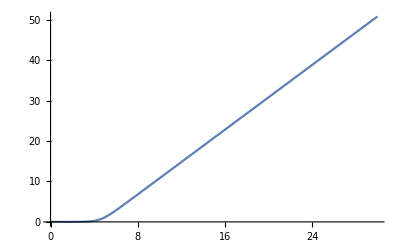

```mathematica
Plot[Log[G11[kphys0*Exp[-Nefolds]]],{Nefolds,0,30}]
```

## γ with decoherence in de Sitter

#### Computation of the integral appearing in the decoherence term

The integral is

```mathematica
FullSimplify[ComplexExpand[Integrate[Exp[2*I*y]*y^(α),{y,1/lEH,x}]],lEH>0&&α>0&&x>0]
```

lEH^(-1-α) ExpIntegralE[-α,-(2 ⅈ)/lEH]-x^(1+α) ExpIntegralE[-α,-2 ⅈ x]

The above can be recasted in

```mathematica
A[α_,x_,lEH_]:=-(-2*I)^(1+α)*(Gamma[1+α,-2*I/lEH]-Gamma[1+α,-2*I*x])
```

We want to expand for small values of x

```mathematica
FullSimplify[Re[ComplexExpand[Normal[Series[A[α,x,lEH],{x,0,3},{lEH,0,1}]]]],lEH>0&&α>0&&x>0]
```

$Aborted

```mathematica
(*The simplification is better performed term by term.*)
FullSimplify[Re[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,11}]]]],α>0&&x>0]
```

(x^(1+α) (14175/(1+α)-(28350 x^2)/(3+α)+(9450 x^4)/(5+α)-(1260 x^6)/(7+α)+(90 x^8)/(9+α)-(4 x^10)/(11+α)))/14175+2^(-1-α) Gamma[1+α] Sin[(π α)/2]

```mathematica
FullSimplify[Im[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,11}]]]],α>0&&x>0]
```

(2 x^(2+α) (2835/(2+α)-(1890 x^2)/(4+α)+(378 x^4)/(6+α)-(36 x^6)/(8+α)+(2 x^8)/(10+α)))/2835-2^(-1-α) α Cos[(π α)/2] Gamma[α]

We will not expand the part in lEH and so we will just give it a name to track it

```mathematica
FullSimplify[Re[ComplexExpand[Normal[Series[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH],{lEH,0,0}]]]],α>0&&lEH>0]
```

-1/2 lEH^-α Sin[2/lEH]

k is the order of expansion in x of the integral

```mathematica
k=11;
```

### γ11

Defining the expanded version of the real part of A that we use in the

```mathematica
ARSimp1I11[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k}]]]],α>0&&x>0]
```

```mathematica
ARSimp2I11[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH]]],α>0&&lEH>0]
```

```mathematica
ARSimp2I11[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[Normal[Series[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH],{lEH,0,0}]]]],α>0&&lEH>0]
```

```mathematica
Simplify[ARSimp2I11[α,x,lEH],α>0&&lEH>0]
```

-2^(-1-α) (Cos[(π α)/2] Im[Gamma[1+α,-(2 ⅈ)/lEH]]+Re[Gamma[1+α,-(2 ⅈ)/lEH]] Sin[(π α)/2])

```mathematica
ARSimpI11[α_,x_,lEH_]:= ARSimp1I11[α,x,lEH]+ARSimp2I11[α,x,lEH]
```

```mathematica
Collect[ARSimpI11[α,x,lEH],x^_,Simplify]
```

x^(1+α)/(1+α)-(2 x^(3+α))/(3+α)+(2 x^(5+α))/(3 (5+α))-(4 x^(7+α))/(45 (7+α))+(2 x^(9+α))/(315 (9+α))-(4 x^(11+α))/(14175 (11+α))+2^(-1-α) (-Cos[(π α)/2] Im[Gamma[1+α,-(2 ⅈ)/lEH]]+(Gamma[1+α]-Re[Gamma[1+α,-(2 ⅈ)/lEH]]) Sin[(π α)/2])

```mathematica
(*Defining the expanded version of the imaginary part of A*)
```

```mathematica
AISimp1I11[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k}]]]],α>0&&x>0]
```

```mathematica
AISimp2I11[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH]]],α>0&&lEH>0]
```

```mathematica
AISimp2I11[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[Normal[Series[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH],{lEH,0,0}]]]],α>0&&lEH>0]
```

```mathematica
(*Same here*)
AISimp2I11[α_,x_,lEH_,Order_]:=FullSimplify[Im[ComplexExpand[Normal[Series[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH],{lEH,0,Order}]]]],α>0&&lEH>0]
```

```mathematica
AISimpI11[α_,x_,lEH_]:=AISimp1I11[α,x,lEH]+AISimp2I11[α,x,lEH]
```

```mathematica
Collect[AISimpI11[α,x,lEH],x^_,Simplify]
```

(2 x^(2+α))/(2+α)-(4 x^(4+α))/(3 (4+α))+(4 x^(6+α))/(15 (6+α))-(8 x^(8+α))/(315 (8+α))+(4 x^(10+α))/(2835 (10+α))-2^(-1-α) (α Cos[(π α)/2] Gamma[α]-Cos[(π α)/2] Re[Gamma[1+α,-(2 ⅈ)/lEH]]+Im[Gamma[1+α,-(2 ⅈ)/lEH]] Sin[(π α)/2])

Quantities used by Jerome for its equations

```mathematica
ARalpha[α_,x_,lEH_,xstar_]:=2^(-(1+α))*Gamma[1+α]*Sin[Pi*α/2]-2^(-(1+α))*Im[Exp[I*Pi*α/2]*Gamma[1+α,(-2 ⅈ)/lEH]]
```

```mathematica
Simplify[ComplexExpand[ARalpha[α,x,lEH,xstar]-ARSimp2I11[α,x,lEH]],α>0&&lEH>0]
```

2^(-1-α) Gamma[1+α] Sin[(π α)/2]

```mathematica
AIalpha[α_,x_,lEH_,xstar_]:=-2^(-(1+α))*Gamma[1+α]*Cos[Pi*α/2]+2^(-(1+α))*(Re[Exp[I*Pi*α/2]*Gamma[1+α,(-2 ⅈ)/lEH]])
```

```mathematica
Simplify[ComplexExpand[AIalpha[α,x,lEH,xstar]-AISimp2I11[α,x,lEH]],α>0&&lEH>0]
```

-2^(-1-α) Cos[(π α)/2] Gamma[1+α]

Computing combinations entering in the expressions for γ11.

First piece for the sum I11^2 + I11^3

```mathematica
(*First bracket is order k+1-p and second, order k+2-p times x, so order k+3-p*)
```

```mathematica
I11231[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[(x^2-1)*Simplify[ARSimpI11[1-p,x,lEH]-ARSimpI11[3-p,x,lEH]+2*AISimpI11[2-p,x,lEH],p>0&&x>0]+2*x*Simplify[AISimpI11[1-p,x,lEH]-AISimpI11[3-p,x,lEH]-2*ARSimpI11[2-p,x,lEH],p>0&&x>0]],x^_,Simplify]
```

We know that the expansion is valid only up to x^k+1 so we set to 0 all the other terms

```mathematica
I11231Temp=Collect[Expand[I11231[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I11231Temp = I11231Temp/.x^b_/;b>k+1->0;
I11231Temp = Collect[Expand[I11231Temp*x^(-p)],x^_,Simplify];
```

We check that only powers of x larger than k+1 were removed so that fot i < k+1 the x^i exactly cancel

```mathematica
Collect[Expand[I11231Temp-I11231[p,x,lEH,xstar]],x^_,Simplify]
```

(2 (-2/(-14+p)-12/(-13+p)-27/(-12+p)) x^(14-p))/14175+(4 x^(16-p))/(14175 (-14+p))

```mathematica
I11231Temp
```

x^(2-p)/(-2+p)+(2 x^(4-p))/(8-6 p+p^2)+(4/(15-3 p)+1/(4-p)) x^(6-p)+(-2/(9 (-8+p))-8/(15 (-7+p))) x^(8-p)+(2/(45 (-10+p))+8/(35 (-9+p))+2/(9 (-8+p))) x^(10-p)+(2/(450-45 p)-2/(525 (-12+p))-16/(567 (-11+p))) x^(12-p)+2^(-4+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-2^(-4+p) x^2 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
I11231[p_,x_,lEH_,xstar_]:=x^(2-p)/(-2+p)+(2 x^(4-p))/(8-6 p+p^2)+(4/(15-3 p)+1/(4-p)) x^(6-p)+(-2/(9 (-8+p))-8/(15 (-7+p))) x^(8-p)+(2/(45 (-10+p))+8/(35 (-9+p))+2/(9 (-8+p))) x^(10-p)+(2/(450-45 p)-2/(525 (-12+p))-16/(567 (-11+p))) x^(12-p)+2^(-4+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-2^(-4+p) x^2 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

Second piece for the sum I11^2 + I11^3

```mathematica
I11232[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[(x^2-1)*Simplify[AISimpI11[1-p,x,lEH]-AISimpI11[3-p,x,lEH]-2*ARSimpI11[2-p,x,lEH],p>0&&x>0]-2*x*Simplify[ARSimpI11[1-p,x,lEH]-ARSimpI11[3-p,x,lEH]+2*AISimpI11[2-p,x,lEH],p>0&&x>0]],x^_,Simplify]
```

```mathematica
I11232Temp=Collect[Expand[I11232[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I11232Temp = I11232Temp/.x^b_/;b>k+1->0;
I11232Temp = Collect[Expand[I11232Temp*x^(-p)],x^_,Simplify]
```

(2 x^(3-p))/(-2+p)+(2 (-19+4 p) x^(5-p))/(3 (-5+p) (-4+p))+(2/(15-3 p)+4/(15 (-7+p))) x^(7-p)+(-4/(35 (-9+p))-4/(9 (-8+p))-4/(15 (-7+p))) x^(9-p)+(8/(567 (-11+p))+4/(45 (-10+p))+4/(35 (-9+p))) x^(11-p)+2^(-3+p) x (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-4+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-4+p) x^2 (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
Collect[Expand[I11232Temp-I11232[p,x,lEH,xstar]],x^_,Simplify]
```

(4 (3/(-13+p)+27/(-12+p)+50/(-11+p)) x^(13-p))/14175-(4 (-68+5 p) x^(15-p))/(14175 (-14+p) (-13+p))

```mathematica
I11232[p_,x_,lEH_,xstar_]:=(2 x^(3-p))/(-2+p)+(2 (-19+4 p) x^(5-p))/(3 (-5+p) (-4+p))+(2/(15-3 p)+4/(15 (-7+p))) x^(7-p)+(-4/(35 (-9+p))-4/(9 (-8+p))-4/(15 (-7+p))) x^(9-p)+(8/(567 (-11+p))+4/(45 (-10+p))+4/(35 (-9+p))) x^(11-p)+2^(-3+p) x (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-4+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-4+p) x^2 (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

Sum the two pieces and multiply by the Sin and the Cos functions

```mathematica
I1123[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[xstar^(p-3)*I11231[p,x,lEH,xstar]*Normal[Series[Cos[2*x],{x,0,k}]]/(2*x^2)+xstar^(p-3)*I11232[p,x,lEH,xstar]*Normal[Series[Sin[2*x],{x,0,k}]]/(2*x^2)],x^_,Simplify]
```

```mathematica
Collect[Expand[ Normal[Series[Cos[2*x],{x,0,10}]]],x^_,Simplify]
```

1-2 x^2+(2 x^4)/3-(4 x^6)/45+(2 x^8)/315-(4 x^10)/14175

```mathematica
I1123Temp=Collect[Expand[I1123[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I1123Temp=I1123Temp/.x^b_/;b>k-1->0;
I1123Temp = Collect[Expand[I1123Temp*x^(-p)],x^_,Simplify];
```

```mathematica
Collect[Expand[I1123[p,x,lEH,xstar]-I1123Temp],x^_,Simplify]
```

((-2182688640+3081685368 p-1735086430 p^2+511595483 p^3-86134300 p^4+8334242 p^5-431110 p^6+9227 p^7) x^(12-p) xstar^(-3+p))/(467775 (-12+p) (-11+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-(4 (-10282734000+10419354840 p-4413899341 p^2+1014952025 p^3-137024395 p^4+10876565 p^5-470584 p^6+8570 p^7) x^(14-p) xstar^(-3+p))/(3274425 (-12+p) (-11+p) (-10+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p))+(4 (2181771900-1659496455 p+516944452 p^2-84526510 p^3+7659300 p^4-364955 p^5+7148 p^6) x^(16-p) xstar^(-3+p))/(16372125 (-12+p) (-11+p) (-10+p) (-9+p) (-8+p) (-7+p) (-5+p))-(4 (-921113424+518795169 p-115840460 p^2+12817580 p^3-702736 p^4+15271 p^5) x^(18-p) xstar^(-3+p))/(442047375 (-12+p) (-11+p) (-10+p) (-9+p) (-8+p) (-7+p))+(8 (-1467585+442929 p-44005 p^2+1441 p^3) x^(20-p) xstar^(-3+p))/(2210236875 (-12+p) (-11+p) (-10+p) (-9+p))

```mathematica
I1123Temp
```

((-3+p) x^(2-p) xstar^(-3+p))/((-4+p) (-2+p))+(x^(4-p) xstar^(-3+p))/(2 (-4+p))-(2 x^(6-p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))+(8 (-6+p) x^(8-p) xstar^(-3+p))/((-10+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-(32 x^(10-p) xstar^(-3+p))/((-12+p) (-10+p) (-9+p) (-7+p) (-5+p) (-4+p) (-2+p))+(x^-p xstar^(-3+p))/(2 (-2+p))+2^(-5+p) xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/x^2 2^(-5+p) xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/9 2^(-4+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/45 2^(-4+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/525 2^(-4+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/22275 2^(-3+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-4+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/15 2^(-3+p) x^3 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/567 2^(-2+p) x^7 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/155925 2^(-2+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/35 2^(-3+p) x^5 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/4455 2^(-3+p) x^9 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
I1123[p_,x_,lEH_,xstar_]:=((-3+p) x^(2-p) xstar^(-3+p))/((-4+p) (-2+p))+(x^(4-p) xstar^(-3+p))/(2 (-4+p))-(2 x^(6-p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))+(8 (-6+p) x^(8-p) xstar^(-3+p))/((-10+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-(32 x^(10-p) xstar^(-3+p))/((-12+p) (-10+p) (-9+p) (-7+p) (-5+p) (-4+p) (-2+p))+(x^-p xstar^(-3+p))/(2 (-2+p))+2^(-5+p) xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/x^2 2^(-5+p) xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/9 2^(-4+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/45 2^(-4+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/525 2^(-4+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/22275 2^(-3+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-4+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/15 2^(-3+p) x^3 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/567 2^(-2+p) x^7 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/155925 2^(-2+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/35 2^(-3+p) x^5 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/4455 2^(-3+p) x^9 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

Last piece is I11^1 which has a simple expression

```mathematica
I111[p_,x_,lEH_,xstar_]:=xstar^(p-3)*(1+x^2)*(x^(2-p)/(2-p)+x^(4-p)/(4-p)-(lEH)^(p-2)/(2-p)-(lEH)^(p-4)/(4-p))/(2*x^2)
```

```mathematica
(*When using Collect put a x^_ instead of simply x*)
I11[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[I1123[p,x,lEH,xstar]+I111[p,x,lEH,xstar]],x^_,Simplify]
```

We now can check if the coefficients afree with the draft

```mathematica
FullSimplify[1/(32 lEH^4 (8-6 p+p^2) x^2)xstar^(-3+p) (-32 lEH^p-64 lEH^(2+p)+16 lEH^p p+16 lEH^(2+p) p-128 lEH^(2+p) Cos[2/lEH]+96 lEH^(2+p) p Cos[2/lEH]-16 lEH^(2+p) p^2 Cos[2/lEH]-2^(2+p) lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[2-p]-2^(2+p) lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[3-p]-2^(3+p) lEH^4 Cos[(p π)/2] Gamma[4-p]+3 2^(1+p) lEH^4 p Cos[(p π)/2] Gamma[4-p]-2^p lEH^4 p^2 Cos[(p π)/2] Gamma[4-p]-64 lEH^(1+p) Sin[2/lEH]+64 lEH^(3+p) Sin[2/lEH]+48 lEH^(1+p) p Sin[2/lEH]-48 lEH^(3+p) p Sin[2/lEH]-8 lEH^(1+p) p^2 Sin[2/lEH]+8 lEH^(3+p) p^2 Sin[2/lEH])]
```

(xstar^(-3+p) (-2^p (-6+p) Cos[(p π)/2] Gamma[4-p]+(8 lEH^(-4+p) (2 (-2+lEH^2 (-4+p)+p)+lEH (-4+p) (-2+p) (-2 lEH Cos[2/lEH]+(-1+lEH^2) Sin[2/lEH])))/(-4+p)))/(32 (-2+p) x^2)

(xstar^(-3+p) (-2^p (-6+p) Cos[(p π)/2] Gamma[4-p]+(8 lEH^(-4+p) (2 (-2+lEH^2 (-4+p)+p)+lEH (-4+p) (-2+p) (-2 lEH Cos[2/lEH]+(-1+lEH^2) Sin[2/lEH])))/(-4+p)))/(32 (-2+p) x^2)

(xstar^(-3+p) (-2^p (-6+p) Cos[(p π)/2] Gamma[4-p]+(8 lEH^(-4+p) (2 (-2+lEH^2 (-4+p)+p)+lEH (-4+p) (-2+p) (-2 lEH Cos[2/lEH]+(-1+lEH^2) Sin[2/lEH])))/(-4+p)))/(32 (-2+p) x^2)

«4 more identical outputs»

```mathematica
Collect[I11[p,x,lEH,xstar],x^_,Simplify]
```

-(2 x^(6-p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))+(8 (-6+p) x^(8-p) xstar^(-3+p))/((-10+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-(32 x^(10-p) xstar^(-3+p))/((-12+p) (-10+p) (-9+p) (-7+p) (-5+p) (-4+p) (-2+p))-1/9 2^(-4+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/45 2^(-4+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/525 2^(-4+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/22275 2^(-3+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/32 xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(32 x^2)xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-4+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/15 2^(-3+p) x^3 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/567 2^(-2+p) x^7 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/155925 2^(-2+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/35 2^(-3+p) x^5 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/4455 2^(-3+p) x^9 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

Checking relation with respect to D11

```mathematica
D11[p_,x_,lEH_,xstar_]:=1/3 2^(-4+p)  xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
Simplify[ComplexExpand[xstar^(-3+p)*( -AIalpha[1-p,x,lEH,xstar]+2*ARalpha[2-p,x,lEH,xstar]+AIalpha[3-p,x,lEH,xstar])/3-D11[p,x,lEH,xstar],Element[xstar,Reals]&&p>0&&lEH>0]]
```

1/3 2^(-4+p) (xstar^2)^(1/2 (-3+p)) (4 (-1+p) Gamma[1-p]+4 Gamma[2-p]-3 Gamma[3-p]+p Gamma[3-p]+Gamma[4-p]) Sin[(p π)/2] (Cos[(-3+p) Arg[xstar]]+ⅈ Sin[(-3+p) Arg[xstar]])

```mathematica
FullSimplify[4 (-1+p) Gamma[1-p]+4 Gamma[2-p]-3 Gamma[3-p]+p Gamma[3-p]+Gamma[4-p]]
```

0

```mathematica
Simplify[1/35 2^(-3+p)xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+6*D11[p,x,lEH,xstar]/35]
```

0

```mathematica
xstar^(-3+p)*Simplify[ComplexExpand[Normal[Series[1/32 (-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]),{lEH,0,1}]]],p>0&&lEH>0]
```

1/32 xstar^(-3+p) (2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]-4 lEH^(-3+p) (lEH (7+lEH^2 (-1+p)-p) Cos[2/lEH]+2 (1+lEH^2 (-3+p)) Sin[2/lEH]))

```mathematica
FullSimplify[2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]]
```

-(2^p (-6+p) Cos[(p π)/2] Gamma[4-p])/(-2+p)

```mathematica
FullSimplify[lEH (7+lEH^2 (-1+p)-p) Cos[2/lEH]+2 (1+lEH^2 (-3+p)) Sin[2/lEH]]
```

lEH (7+lEH^2 (-1+p)-p) Cos[2/lEH]+2 (1+lEH^2 (-3+p)) Sin[2/lEH]

```mathematica
FullSimplify[ComplexExpand[- 2^(-4+p)  (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-(   ARalpha[1-p,x,lEH,xstar]+2*AIalpha[2-p,x,lEH,xstar]-ARalpha[3-p,x,lEH,xstar]),p>0&&lEH>0]]
```

0

#### Extract pieces with and without x^p

```mathematica
(*We extract the part of powers of x which is independent of p and give it a name for further computations*)
```

Piece which does not contain x^p

```mathematica
λ11Exact[p_,x_,lEH_,xstar_]:=xstar^(p-3)*(1+x^2)*(-(lEH)^(p-2)/(2-p)-(lEH)^(p-4)/(4-p))/(2*x^2)+xstar^(p-3)*(1/16 x^2 (-2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]+2^p Cos[(p π)/2] Gamma[4-p]-2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/16 (2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/8 x (2 lEH^(-3+p) ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p (-7+p) Gamma[3-p] Sin[(p π)/2]))*Cos[2*x]/(2*x^2)+xstar^(p-3)*(1/8 x (2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/16 (lEH^(-3+p) (-2 (-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]+4 lEH (-7+p) Sin[2/lEH])-2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]-2^p (-7+p) Gamma[3-p] Sin[(p π)/2])+1/16 x^2 (2 lEH^(-3+p) ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p (-7+p) Gamma[3-p] Sin[(p π)/2]))*Sin[2*x]/(2*x^2)
```

```mathematica
μ11[p_,x_,lEH_,xstar_]:=-(2 x^(6-p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))+(8 (-6+p) x^(8-p) xstar^(-3+p))/((-10+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-(32 x^(10-p) xstar^(-3+p))/((-12+p) (-10+p) (-9+p) (-7+p) (-5+p) (-4+p) (-2+p))
```

```mathematica
λ11[p_,x_,lEH_,xstar_]:=-1/9 2^(-4+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/45 2^(-4+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/525 2^(-4+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/22275 2^(-3+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/32 xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(32 x^2)xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-4+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/15 2^(-3+p) x^3 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/567 2^(-2+p) x^7 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/155925 2^(-2+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/35 2^(-3+p) x^5 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/4455 2^(-3+p) x^9 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
Collect[1/(32 lEH^4 (-4+p) (-2+p))xstar^(-3+p) (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])),lEH^_,FullSimplify]
```

(lEH^(-4+p) xstar^(-3+p))/(2 (-4+p))+(lEH^(-2+p) xstar^(-3+p) (4+(-7+p) (-2+p) Cos[2/lEH]))/(8 (-2+p))-2^(-5+p) (-6+p) (-3+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-1/4 lEH^(-3+p) xstar^(-3+p) Sin[2/lEH]+1/16 lEH^(-1+p) (-6+p) (-3+p) xstar^(-3+p) Sin[2/lEH]

```mathematica
(*Check that there is no copy paste mistake*)
I11[p,x,lEH,xstar]- λ11[p,x,lEH,xstar]-μ11[p,x,lEH,xstar]
```

0

### γ12

Compute useful combinations for the integrals I12 and I22

```mathematica
(*Defining the expanded version of the real part of A at the correct order for I12*)
ARSimp1I12[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k+1}]]]],α>0&&x>0]
```

```mathematica
ARSimp2I12[α_,x_,lEH_]:=FullSimplify[Re[ComplexExpand[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH]]],α>0&&lEH>0]
```

```mathematica
ARSimpI12[α_,x_,lEH_]:= ARSimp1I12[α,x,lEH]+ARSimp2I12[α,x,lEH]
```

```mathematica
(2 x^(2+α))/(2+α)+(4 x^(4+α) (-51975/(4+α)+(10395 x^2)/(6+α)-(990 x^4)/(8+α)+(55 x^6)/(10+α)-(2 x^8)/(12+α)))/155925-2^(-1-α) α Cos[(π α)/2] Gamma[α]-1/4 lEH^-α (-2 Cos[2/lEH]+lEH α Sin[2/lEH])
```

```mathematica
Collect[ARSimpI12[α,x,lEH],x^_,Simplify]
```

x^(1+α)/(1+α)-(2 x^(3+α))/(3+α)+(2 x^(5+α))/(3 (5+α))-(4 x^(7+α))/(45 (7+α))+(2 x^(9+α))/(315 (9+α))-(4 x^(11+α))/(14175 (11+α))+2^(-1-α) (-Cos[(π α)/2] Im[Gamma[1+α,-(2 ⅈ)/lEH]]+(Gamma[1+α]-Re[Gamma[1+α,-(2 ⅈ)/lEH]]) Sin[(π α)/2])

```mathematica
(*Defining the expanded version of the imaginary part of A*)
```

```mathematica
AISimp1I12[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k+1}]]]],α>0&&x>0]
```

```mathematica
AISimp2I12[α_,x_,lEH_]:=FullSimplify[Im[ComplexExpand[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH]]],α>0&&lEH>0]
```

```mathematica
AISimpI12[α_,x_,lEH_]:=AISimp1I12[α,x,lEH]+AISimp2I12[α,x,lEH]
```

```mathematica
Collect[AISimpI12[α,x,lEH],x^_,Simplify]
```

(2 x^(2+α))/(2+α)-(4 x^(4+α))/(3 (4+α))+(4 x^(6+α))/(15 (6+α))-(8 x^(8+α))/(315 (8+α))+(4 x^(10+α))/(2835 (10+α))-(8 x^(12+α))/(155925 (12+α))-2^(-1-α) (α Cos[(π α)/2] Gamma[α]-Cos[(π α)/2] Re[Gamma[1+α,-(2 ⅈ)/lEH]]+Im[Gamma[1+α,-(2 ⅈ)/lEH]] Sin[(π α)/2])

```mathematica
(*First bracket is order k+2-p (a priori but this order vanishes) and second bracket order k+2-p times x so order k+3-p*)
I12231[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[(1-2*x^2)*(Simplify[-ARSimpI12[1-p,x,lEH]+ARSimpI12[3-p,x,lEH]-2*AISimpI12[2-p,x,lEH],p>0&&x>0])-x*(2-x^2)*(Simplify[-AISimpI12[1-p,x,lEH]+AISimpI12[3-p,x,lEH]+2*ARSimpI12[2-p,x,lEH],p>0&&x>0])],x^_,Simplify]
```

```mathematica
I12231Temp=Collect[Expand[I12231[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I12231Temp = I12231Temp/.x^b_/;b>k+2->0;
I12231Temp= Collect[Expand[I12231Temp*x^(-p)],x^_,Simplify];
```

```mathematica
I12231Temp
```

x^(2-p)/(-2+p)+(1/(-4+p)-2/(-2+p)) x^(4-p)+(-4/(3 (-5+p))-2/(-4+p)) x^(6-p)+(2/(72-9 p)-8/(15 (-7+p))+2/(3 (-5+p))) x^(8-p)+2/315 (7/(-10+p)+36/(-9+p)+70/(-8+p)+42/(-7+p)) x^(10-p)+(-2/(525 (-12+p))-16/(567 (-11+p))-4/(45 (-10+p))-4/(35 (-9+p))) x^(12-p)+2^(-4+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-2^(-3+p) x^2 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-4+p) x^3 (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
I12231[p_,x_,lEH_,xstar_]:=x^(2-p)/(-2+p)+(1/(-4+p)-2/(-2+p)) x^(4-p)+(-4/(3 (-5+p))-2/(-4+p)) x^(6-p)+(2/(72-9 p)-8/(15 (-7+p))+2/(3 (-5+p))) x^(8-p)+2/315 (7/(-10+p)+36/(-9+p)+70/(-8+p)+42/(-7+p)) x^(10-p)+(-2/(525 (-12+p))-16/(567 (-11+p))-4/(45 (-10+p))-4/(35 (-9+p))) x^(12-p)+2^(-4+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-2^(-3+p) x^2 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-4+p) x^3 (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
I12232[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[(1-2*x^2)*(Simplify[-AISimpI12[1-p,x,lEH]+AISimpI12[3-p,x,lEH]+2*ARSimpI12[2-p,x,lEH],p>0&&x>0])+x*(2-x^2)*(Simplify[-ARSimpI12[1-p,x,lEH]+ARSimpI12[3-p,x,lEH]-2*AISimpI12[2-p,x,lEH],p>0&&x>0])],x^_,Simplify]
```

```mathematica
I12232Temp=Collect[Expand[I12232[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I12232Temp=I12232Temp/.x^b_/;b>k+2->0;
I12232Temp= Collect[Expand[I12232Temp*x^(-p)],x^_,Simplify];
```

```mathematica
I12232Temp
```

(2 x^(3-p))/(-2+p)+(1/(2-p)+2/(3 (-5+p))+2/(-4+p)) x^(5-p)+(1/(4-p)+4/(15 (-7+p))-4/(3 (-5+p))) x^(7-p)+(4/(72-9 p)-4/(35 (-9+p))-8/(15 (-7+p))) x^(9-p)+(8/(567 (-11+p))+4/(45 (-10+p))+8/(35 (-9+p))+2/(9 (-8+p))) x^(11-p)+(-4/(4455 (-13+p))-4/(525 (-12+p))-16/(567 (-11+p))-2/(45 (-10+p))) x^(13-p)+2^(-3+p) x (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-2^(-4+p) x^3 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-4+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x^2 (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
I12232[p_,x_,lEH_,xstar_]:=(2 x^(3-p))/(-2+p)+(1/(2-p)+2/(3 (-5+p))+2/(-4+p)) x^(5-p)+(1/(4-p)+4/(15 (-7+p))-4/(3 (-5+p))) x^(7-p)+(4/(72-9 p)-4/(35 (-9+p))-8/(15 (-7+p))) x^(9-p)+(8/(567 (-11+p))+4/(45 (-10+p))+8/(35 (-9+p))+2/(9 (-8+p))) x^(11-p)+(-4/(4455 (-13+p))-4/(525 (-12+p))-16/(567 (-11+p))-2/(45 (-10+p))) x^(13-p)+2^(-3+p) x (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-2^(-4+p) x^3 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-4+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x^2 (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
I1223[p_,x_,lEH_,xstar_]:=xstar^(p-3)*I12231[p,x,lEH,xstar]*Normal[Series[Cos[2*x],{x,0,k+1}]]/(2*x^3)+xstar^(p-3)*I12232[p,x,lEH,xstar]*Normal[Series[Sin[2*x],{x,0,k+1}]]/(2*x^3)
```

```mathematica
I1223Temp=Collect[Expand[I1223[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I1223Temp=I1223Temp/.x^b_/;b>k-1->0;
I1223Temp= Collect[Expand[I1223Temp*x^(-p)],x^_,Simplify];
```

```mathematica
I1223Temp
```

(x^(-1-p) xstar^(-3+p))/(2 (-2+p))+(x^(1-p) xstar^(-3+p))/(2 (-4+p))-((-6+p) x^(5-p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))+(4 (-6+p) x^(7-p) xstar^(-3+p))/((-10+p) (-7+p) (-5+p) (-4+p) (-2+p))-(16 x^(9-p) xstar^(-3+p))/((-12+p) (-9+p) (-7+p) (-5+p) (-4+p) (-2+p))+1/x^3 2^(-5+p) xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/9 2^(-3+p) x^3 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/15 2^(-4+p) x^5 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/525 2^(-2+p) x^7 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/8505 2^(-2+p) x^9 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/467775 2^(-1+p) x^11 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/7 2^(-4+p) x^4 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/495 2^(-4+p) x^8 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/467775 23 2^(-3+p) x^10 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/467775 2^(-3+p) x^12 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-5+p) xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/5 2^(-4+p) x^2 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/81 2^(-3+p) x^6 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
I1223[p_,x_,lEH_,xstar_]:=(x^(-1-p) xstar^(-3+p))/(2 (-2+p))+(x^(1-p) xstar^(-3+p))/(2 (-4+p))-((-6+p) x^(5-p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))+(4 (-6+p) x^(7-p) xstar^(-3+p))/((-10+p) (-7+p) (-5+p) (-4+p) (-2+p))-(16 x^(9-p) xstar^(-3+p))/((-12+p) (-9+p) (-7+p) (-5+p) (-4+p) (-2+p))+1/x^3 2^(-5+p) xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/9 2^(-3+p) x^3 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/15 2^(-4+p) x^5 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/525 2^(-2+p) x^7 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/8505 2^(-2+p) x^9 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/467775 2^(-1+p) x^11 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/7 2^(-4+p) x^4 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/495 2^(-4+p) x^8 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/467775 23 2^(-3+p) x^10 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/467775 2^(-3+p) x^12 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-5+p) xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/5 2^(-4+p) x^2 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/81 2^(-3+p) x^6 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
I121[p_,x_,lEH_,xstar_]:=xstar^(p-3)*(x^(2-p)/(2-p)+x^(4-p)/(4-p)-(lEH)^(p-2)/(2-p)-(lEH)^(p-4)/(4-p))/(2*x^3)
```

```mathematica
I12[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[I1223[p,x,lEH,xstar]+I121[p,x,lEH,xstar]],x^_,Simplify]
```

```mathematica
Simplify[(6 xstar^(-3+p))/((-8+p) (-5+p) (-2+p))-(p xstar^(-3+p))/((-8+p) (-5+p) (-2+p))]
```

-((-6+p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))

```mathematica
(*When using Collect put a x^_ instead of simply x*)
Collect[I12[p,x,lEH,xstar],x^_]
```

-(16 x^(9-p) xstar^(-3+p))/((-12+p) (-9+p) (-7+p) (-5+p) (-4+p) (-2+p))+x^(5-p) ((6 xstar^(-3+p))/((-8+p) (-5+p) (-2+p))-(p xstar^(-3+p))/((-8+p) (-5+p) (-2+p)))+x^(7-p) (-(24 xstar^(-3+p))/((-10+p) (-7+p) (-5+p) (-4+p) (-2+p))+(4 p xstar^(-3+p))/((-10+p) (-7+p) (-5+p) (-4+p) (-2+p)))-1/3 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-1/3 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-1/3 2^(-5+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-1/3 2^(-3+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+1/3 2^(-3+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-7/3 2^(-5+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/3 2^(-5+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/3 2^(-3+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/3 2^(-3+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/3 2^(-5+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/x^3((lEH^(-4+p) xstar^(-3+p))/(2 (-4+p))+(lEH^(-2+p) xstar^(-3+p))/(2 (-2+p))-3 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+2^(-3+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-2^(-5+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]+2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^(-5+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(-3+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(-3+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(-5+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^5 (1/5 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-1/15 2^(-2+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+1/15 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]-1/15 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]-1/15 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]-1/15 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]-1/15 2^(-2+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/15 2^(-2+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/15 2^(-4+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^3 (-1/3 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+1/9 2^(-1+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-1/9 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]+1/9 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+1/9 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+1/9 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+1/9 2^(-1+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/9 2^(-1+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/9 2^(-3+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^9 ((2^p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p])/2835-(2^p p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p])/8505+(2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p])/8505-(2^p xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]])/8505-(2^p xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]])/8505-(2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]])/8505-(2^p xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/8505-(2^p xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/8505-(2^(-2+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/8505)+x^7 (-1/175 2^p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+1/525 2^p p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-1/525 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]+1/525 2^p xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+1/525 2^p xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+1/525 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+1/525 2^p xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/525 2^p xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/525 2^(-2+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^11 (-(2^(1+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p])/155925+(2^(1+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p])/467775-(2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p])/467775+(2^(1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]])/467775+(2^(1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]])/467775+(2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]])/467775+(2^(1+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775+(2^(1+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775+(2^(-1+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775)+x^4 (1/7 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+1/7 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+1/7 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+1/7 2^(-2+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-1/7 2^(-2+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+2^(-4+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]-1/7 2^(-4+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]-1/7 2^(-2+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/7 2^(-2+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/7 2^(-4+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^8 (1/495 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+1/495 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+1/495 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+1/495 2^(-2+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-1/495 2^(-2+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+7/495 2^(-4+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]-1/495 2^(-4+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]-1/495 2^(-2+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/495 2^(-2+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/495 2^(-4+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^2 (-1/5 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-1/5 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-1/5 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-1/5 2^(-2+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+1/5 2^(-2+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-7/5 2^(-4+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/5 2^(-4+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/5 2^(-2+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/5 2^(-2+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/5 2^(-4+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^12 ((2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]])/467775+(2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]])/467775+(2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]])/467775+(2^(-1+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2])/467775-(2^(-1+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2])/467775+(2^(-3+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2])/66825-(2^(-3+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2])/467775-(2^(-1+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775-(2^(-1+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775-(2^(-3+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775)+x^10 (-(23 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]])/467775-(23 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]])/467775-(23 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]])/467775-(23 2^(-1+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2])/467775+(23 2^(-1+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2])/467775-(23 2^(-3+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2])/66825+(23 2^(-3+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2])/467775+(23 2^(-1+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775+(23 2^(-1+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775+(23 2^(-3+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775)+x^6 (-1/81 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-1/81 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-1/81 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-1/81 2^(-1+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+1/81 2^(-1+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-7/81 2^(-3+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/81 2^(-3+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/81 2^(-1+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/81 2^(-1+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/81 2^(-3+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

Comparaison with coefficient times B11

```mathematica
FullSimplify[ComplexExpand[((lEH^(-4+p) xstar^(-3+p))/(2 (-4+p))+(lEH^(-2+p) xstar^(-3+p))/(2 (-2+p))-3 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+2^(-3+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-2^(-5+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]+2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^(-5+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(-3+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(-3+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(-5+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-xstar^(-3+p)*(   -ARalpha[1-p,x,lEH,xstar]-2*AIalpha[2-p,x,lEH,xstar]+ARalpha[3-p,x,lEH,xstar])/2,p>0&&lEH>0]]
```

(ⅇ^(ⅈ (-3+p) Arg[xstar]) (lEH^2)^(p/2) (xstar^2)^(1/2 (-3+p)) Sign[lEH]^(-4+p) (-2+p+lEH^2 (-4+p) Sign[lEH]^2))/(2 lEH^4 (-4+p) (-2+p))

Comparaison with coefficient times D11

```mathematica
FullSimplify[ComplexExpand[-1/81 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-1/81 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-1/81 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-1/81 2^(-1+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+1/81 2^(-1+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-7/81 2^(-3+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/81 2^(-3+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/81 2^(-1+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/81 2^(-1+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/81 2^(-3+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2*xstar^(-3+p)*( -  AIalpha[1-p,x,lEH,xstar]+2*ARalpha[2-p,x,lEH,xstar]+AIalpha[3-p,x,lEH,xstar])/3/27,p>0&&lEH>0]]
```

0

Comparaison with coefficient times F11

```mathematica
FullSimplify[ComplexExpand[1/5 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-1/15 2^(-2+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+1/15 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]-1/15 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]-1/15 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]-1/15 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]-1/15 2^(-2+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/15 2^(-2+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/15 2^(-4+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-3*xstar^(-3+p)*( ARalpha[1-p,x,lEH,xstar]+2*AIalpha[2-p,x,lEH,xstar]-ARalpha[3-p,x,lEH,xstar])/9/5,p>0&&lEH>0]]
```

0

#### Extract part with and without x^p

```mathematica
λ12Exact[p_,x_,lEH_,xstar_]:=xstar^(p-3)*(-(lEH)^(p-2)/(2-p)-(lEH)^(p-4)/(4-p))/(2*x^3)+xstar^(p-3)*(1/8 x^2 (-2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]+2^p Cos[(p π)/2] Gamma[4-p]-2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/16 (2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/16 x^3 (lEH^(-3+p) (-2 (-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]+4 lEH (-7+p) Sin[2/lEH])-2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]-2^p (-7+p) Gamma[3-p] Sin[(p π)/2])+1/8 x (2 lEH^(-3+p) ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p (-7+p) Gamma[3-p] Sin[(p π)/2]))*Cos[2*x]/(2*x^3)+xstar^(p-3)*(1/16 x^3 (-2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]+2^p Cos[(p π)/2] Gamma[4-p]-2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/8 x (2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/16 (lEH^(-3+p) (-2 (-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]+4 lEH (-7+p) Sin[2/lEH])-2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]-2^p (-7+p) Gamma[3-p] Sin[(p π)/2])+1/8 x^2 (2 lEH^(-3+p) ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p (-7+p) Gamma[3-p] Sin[(p π)/2]))*Sin[2*x]/(2*x^3)
```

```mathematica
μ12[p_,x_,lEH_,xstar_]:=-(16 x^(9-p) xstar^(-3+p))/((-12+p) (-9+p) (-7+p) (-5+p) (-4+p) (-2+p))+x^(5-p) ((6 xstar^(-3+p))/((-8+p) (-5+p) (-2+p))-(p xstar^(-3+p))/((-8+p) (-5+p) (-2+p)))+x^(7-p) (-(24 xstar^(-3+p))/((-10+p) (-7+p) (-5+p) (-4+p) (-2+p))+(4 p xstar^(-3+p))/((-10+p) (-7+p) (-5+p) (-4+p) (-2+p)))
```

```mathematica
λ12[p_,x_,lEH_,xstar_]:=-1/3 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-1/3 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-1/3 2^(-5+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-1/3 2^(-3+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+1/3 2^(-3+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-7/3 2^(-5+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/3 2^(-5+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/3 2^(-3+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/3 2^(-3+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/3 2^(-5+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/x^3((lEH^(-4+p) xstar^(-3+p))/(2 (-4+p))+(lEH^(-2+p) xstar^(-3+p))/(2 (-2+p))-3 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+2^(-3+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-2^(-5+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]+2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^(-5+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(-3+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(-3+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(-5+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^5 (1/5 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-1/15 2^(-2+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+1/15 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]-1/15 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]-1/15 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]-1/15 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]-1/15 2^(-2+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/15 2^(-2+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/15 2^(-4+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^3 (-1/3 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+1/9 2^(-1+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-1/9 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]+1/9 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+1/9 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+1/9 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+1/9 2^(-1+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/9 2^(-1+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/9 2^(-3+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^9 ((2^p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p])/2835-(2^p p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p])/8505+(2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p])/8505-(2^p xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]])/8505-(2^p xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]])/8505-(2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]])/8505-(2^p xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/8505-(2^p xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/8505-(2^(-2+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/8505)+x^7 (-1/175 2^p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]+1/525 2^p p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p]-1/525 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p]+1/525 2^p xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+1/525 2^p xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+1/525 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+1/525 2^p xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/525 2^p xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/525 2^(-2+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^11 (-(2^(1+p) xstar^(-3+p) Cos[(p π)/2] Gamma[2-p])/155925+(2^(1+p) p xstar^(-3+p) Cos[(p π)/2] Gamma[2-p])/467775-(2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Gamma[4-p])/467775+(2^(1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]])/467775+(2^(1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]])/467775+(2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]])/467775+(2^(1+p) xstar^(-3+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775+(2^(1+p) xstar^(-3+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775+(2^(-1+p) xstar^(-3+p) Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775)+x^4 (1/7 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+1/7 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+1/7 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+1/7 2^(-2+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-1/7 2^(-2+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+2^(-4+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]-1/7 2^(-4+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]-1/7 2^(-2+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/7 2^(-2+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/7 2^(-4+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^8 (1/495 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+1/495 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+1/495 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+1/495 2^(-2+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-1/495 2^(-2+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+7/495 2^(-4+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]-1/495 2^(-4+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]-1/495 2^(-2+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/495 2^(-2+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-1/495 2^(-4+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^2 (-1/5 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-1/5 2^(-2+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-1/5 2^(-4+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-1/5 2^(-2+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+1/5 2^(-2+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-7/5 2^(-4+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/5 2^(-4+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/5 2^(-2+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/5 2^(-2+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/5 2^(-4+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+x^12 ((2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]])/467775+(2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]])/467775+(2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]])/467775+(2^(-1+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2])/467775-(2^(-1+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2])/467775+(2^(-3+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2])/66825-(2^(-3+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2])/467775-(2^(-1+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775-(2^(-1+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775-(2^(-3+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775)+x^10 (-(23 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]])/467775-(23 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]])/467775-(23 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]])/467775-(23 2^(-1+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2])/467775+(23 2^(-1+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2])/467775-(23 2^(-3+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2])/66825+(23 2^(-3+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2])/467775+(23 2^(-1+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775+(23 2^(-1+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775+(23 2^(-3+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/467775)+x^6 (-1/81 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-1/81 2^(-1+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-1/81 2^(-3+p) xstar^(-3+p) Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-1/81 2^(-1+p) xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]+1/81 2^(-1+p) p xstar^(-3+p) Gamma[1-p] Sin[(p π)/2]-7/81 2^(-3+p) xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/81 2^(-3+p) p xstar^(-3+p) Gamma[3-p] Sin[(p π)/2]+1/81 2^(-1+p) xstar^(-3+p) Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/81 2^(-1+p) xstar^(-3+p) Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+1/81 2^(-3+p) xstar^(-3+p) Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
(*Check that there is no copy paste mistake*)
Simplify[I12[p,x,lEH,xstar]- λ12[p,x,lEH,xstar]-μ12[p,x,lEH,xstar]]
```

0

### γ22

```mathematica
(*Defining the expanded version of the real part of A at the correct order for I12*)
ARSimp1I22[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k+2}]]]],α>0&&x>0]
```

```mathematica
ARSimp2I22[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH]]],α>0&&lEH>0]
```

```mathematica
ARSimpI22[α_,x_,lEH_]:= ARSimp1I22[α,x,lEH]+ARSimp2I22[α,x,lEH]
```

```mathematica
Collect[ARSimpI22[α,x,lEH],x^_]
```

x^(1+α)/(1+α)-(2 x^(3+α))/(3+α)+(2 x^(5+α))/(3 (5+α))-(4 x^(7+α))/(45 (7+α))+(2 x^(9+α))/(315 (9+α))-(4 x^(11+α))/(14175 (11+α))+(4 x^(13+α))/(467775 (13+α))-2^(-1-α) Cos[(π α)/2] Im[Gamma[1+α,-(2 ⅈ)/lEH]]+2^(-1-α) Gamma[1+α] Sin[(π α)/2]-2^(-1-α) Re[Gamma[1+α,-(2 ⅈ)/lEH]] Sin[(π α)/2]

```mathematica
(*Defining the expanded version of the imaginary part of A*)
AISimp1I22[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k+2}]]]],α>0&&x>0]
```

```mathematica
AISimp2I22[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[(-2*I)^(-(1+α))*Gamma[1+α,-2*I/lEH]]],α>0&&lEH>0]
```

```mathematica
AISimpI22[α_,x_,lEH_]:=AISimp1I22[α,x,lEH]+AISimp2I22[α,x,lEH]
```

```mathematica
Collect[AISimpI22[α,x,lEH],x^_]
```

(2 x^(2+α))/(2+α)-(4 x^(4+α))/(3 (4+α))+(4 x^(6+α))/(15 (6+α))-(8 x^(8+α))/(315 (8+α))+(4 x^(10+α))/(2835 (10+α))-(8 x^(12+α))/(155925 (12+α))-2^(-1-α) α Cos[(π α)/2] Gamma[α]+2^(-1-α) Cos[(π α)/2] Re[Gamma[1+α,-(2 ⅈ)/lEH]]-2^(-1-α) Im[Gamma[1+α,-(2 ⅈ)/lEH]] Sin[(π α)/2]

```mathematica
(*For I22*)
```

```mathematica
(*First bracket is valid up to order k+3-p and second up to order k + 4 - p times x so order k + 5 -p. We have to cut at order k + 3 -p. *)
I22231[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[(3-6x^2+2*x^4)*Simplify[-ARSimpI22[1-p,x,lEH]+ARSimpI22[3-p,x,lEH]-2*AISimpI22[2-p,x,lEH],p>0&&x>0]-(6*x-4*x^3)*Simplify[-AISimpI22[1-p,x,lEH]+AISimpI22[3-p,x,lEH]+2*ARSimpI22[2-p,x,lEH],p>0&&x>0]],x^_,Simplify]
```

```mathematica
I22231Temp=Collect[Expand[I22231[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I22231Temp=I22231Temp/.x^b_/;b>k+3->0;
I22231Temp= Collect[Expand[I22231Temp*x^(-p)],x^_,Simplify];
```

```mathematica
Collect[Expand[I22231[p,x,lEH,xstar]-I22231Temp],x^_,Simplify]
```

(4 (1/(16-p)-8/(-15+p)-44/(-14+p)-140/(-13+p)-297/(-12+p)) x^(16-p))/155925+(8 (7702-1009 p+33 p^2) x^(18-p))/(467775 (-16+p) (-15+p) (-14+p))-(8 x^(20-p))/(467775 (-16+p))

```mathematica
I22231Temp
```

(3 x^(2-p))/(-2+p)-(3 (-6+p) x^(4-p))/(8-6 p+p^2)+(-4/(-5+p)-6/(-4+p)+2/(-2+p)) x^(6-p)+(2/(24-3 p)-8/(5 (-7+p))+8/(3 (-5+p))+2/(-4+p)) x^(8-p)+2/105 (7/(-10+p)+36/(-9+p)+70/(-8+p)+56/(-7+p)) x^(10-p)+(-2/(175 (-12+p))-16/(189 (-11+p))-4/(15 (-10+p))-16/(35 (-9+p))-4/(9 (-8+p))) x^(12-p)+(4 (22/(-14+p)+210/(-13+p)+891/(-12+p)+2200/(-11+p)+3465/(-10+p)) x^(14-p))/155925+3 2^(-4+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-3 2^(-3+p) x^2 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x^4 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-3 2^(-3+p) x (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-2+p) x^3 (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
I22231[p_,x_,lEH_,xstar_]:=(3 x^(2-p))/(-2+p)-(3 (-6+p) x^(4-p))/(8-6 p+p^2)+(-4/(-5+p)-6/(-4+p)+2/(-2+p)) x^(6-p)+(2/(24-3 p)-8/(5 (-7+p))+8/(3 (-5+p))+2/(-4+p)) x^(8-p)+2/105 (7/(-10+p)+36/(-9+p)+70/(-8+p)+56/(-7+p)) x^(10-p)+(-2/(175 (-12+p))-16/(189 (-11+p))-4/(15 (-10+p))-16/(35 (-9+p))-4/(9 (-8+p))) x^(12-p)+(4 (22/(-14+p)+210/(-13+p)+891/(-12+p)+2200/(-11+p)+3465/(-10+p)) x^(14-p))/155925+3 2^(-4+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-3 2^(-3+p) x^2 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x^4 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-3 2^(-3+p) x (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-2+p) x^3 (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
(*Here first bracket is valid up to order k+4-p and second up to order k + 3 - p times x so order k + 4 -p. We have to cut at order k + 4 -p but to be coherent with the above we cut at k + 3 -p. *)
I22232[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[(3-6x^2+2*x^4)*Simplify[-AISimpI22[1-p,x,lEH]+AISimpI22[3-p,x,lEH]+2*ARSimpI22[2-p,x,lEH],p>0&&x>0]+(6*x-4*x^3)*Simplify[-ARSimpI22[1-p,x,lEH]+ARSimpI22[3-p,x,lEH]-2*AISimpI22[2-p,x,lEH],p>0&&x>0]],x^_,Simplify]
```

```mathematica
I22232Temp=Collect[Expand[I22232[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I22232Temp=I22232Temp/.x^b_/;b>k+3->0;
I22232Temp= Collect[Expand[I22232Temp*x^(-p)],x^_,Simplify];
```

```mathematica
(*WARNING : This line crashes the script for no reason*)
Collect[Expand[I22232[p,x,lEH,xstar]-I22232Temp],x^_,Simplify]
```

(8 (2/(-15+p)+22/(-14+p)+105/(-13+p)+297/(-12+p)+550/(-11+p)) x^(15-p))/155925+(8 (-3/(-16+p)-12/(-15+p)-44/(-14+p)-105/(-13+p)) x^(17-p))/467775+(16 (-47+3 p) x^(19-p))/(467775 (-16+p) (-15+p))

```mathematica
I22232Temp
```

(6 x^(3-p))/(-2+p)+(2/(-5+p)+6/(-4+p)-4/(-2+p)) x^(5-p)+(4/(5 (-7+p))-4/(-5+p)-4/(-4+p)) x^(7-p)+(4/(24-3 p)-12/(35 (-9+p))-8/(5 (-7+p))+4/(3 (-5+p))) x^(9-p)+4/945 (10/(-11+p)+63/(-10+p)+162/(-9+p)+210/(-8+p)+126/(-7+p)) x^(11-p)+(-4/(1485 (-13+p))-4/(175 (-12+p))-16/(189 (-11+p))-8/(45 (-10+p))-8/(35 (-9+p))) x^(13-p)+3 2^(-3+p) x (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-2^(-2+p) x^3 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+3 2^(-4+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-3 2^(-3+p) x^2 (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x^4 (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
I22232[p_,x_,lEH_,xstar_]:=(6 x^(3-p))/(-2+p)+(2/(-5+p)+6/(-4+p)-4/(-2+p)) x^(5-p)+(4/(5 (-7+p))-4/(-5+p)-4/(-4+p)) x^(7-p)+(4/(24-3 p)-12/(35 (-9+p))-8/(5 (-7+p))+4/(3 (-5+p))) x^(9-p)+4/945 (10/(-11+p)+63/(-10+p)+162/(-9+p)+210/(-8+p)+126/(-7+p)) x^(11-p)+(-4/(1485 (-13+p))-4/(175 (-12+p))-16/(189 (-11+p))-8/(45 (-10+p))-8/(35 (-9+p))) x^(13-p)+3 2^(-3+p) x (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-2^(-2+p) x^3 (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+3 2^(-4+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-3 2^(-3+p) x^2 (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+2^(-3+p) x^4 (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
I2223[p_,x_,lEH_,xstar_]:=xstar^(p-3)*(I22231[p,x,lEH,xstar]*Normal[Series[Cos[2*x],{x,0,k+2}]]/2/x^4+I22232[p,x,lEH,xstar]*Normal[Series[Sin[2*x],{x,0,k+2}]]/2/x^4)
```

```mathematica
I2223Temp=Collect[Expand[I2223[p,x,lEH,xstar]*x^(+p)],x^_,Simplify];
I2223Temp=I2223Temp/.x^b_/;b>k-1->0;
I2223Temp= Collect[Expand[I2223Temp*x^(-p)],x^_,Simplify];
```

```mathematica
I2223Temp
```

(3 x^(-2-p) xstar^(-3+p))/(2 (-2+p))-((-6+p) x^(4-p) xstar^(-3+p))/((-8+p) (-2+p))+(4 (-6+p) x^(6-p) xstar^(-3+p))/((-10+p) (-5+p) (-4+p) (-2+p))-(16 x^(8-p) xstar^(-3+p))/((-12+p) (-7+p) (-5+p) (-4+p) (-2+p))+(64 x^(10-p) xstar^(-3+p))/((-14+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))+(3 x^-p xstar^(-3+p))/(2 (-4+p))+1/x^4 3 2^(-5+p) xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/3 2^(-3+p) x^2 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-4+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/75 2^(-2+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/945 2^(-2+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/675675 17 2^(-1+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/675675 2^(-2+p) x^12 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/5 2^(-3+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/27 2^(-2+p) x^5 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/4095 2^(-2+p) x^9 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/6081075 29 2^(-1+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/6081075 2^(-1+p) x^13 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/7 2^(-2+p) x^3 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/495 2^(-1+p) x^7 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

```mathematica
I2223[p_,x_,lEH_,xstar_]:=(3 x^(-2-p) xstar^(-3+p))/(2 (-2+p))-((-6+p) x^(4-p) xstar^(-3+p))/((-8+p) (-2+p))+(4 (-6+p) x^(6-p) xstar^(-3+p))/((-10+p) (-5+p) (-4+p) (-2+p))-(16 x^(8-p) xstar^(-3+p))/((-12+p) (-7+p) (-5+p) (-4+p) (-2+p))+(64 x^(10-p) xstar^(-3+p))/((-14+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))+(3 x^-p xstar^(-3+p))/(2 (-4+p))+1/x^4 3 2^(-5+p) xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/3 2^(-3+p) x^2 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-4+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/75 2^(-2+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/945 2^(-2+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/675675 17 2^(-1+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/675675 2^(-2+p) x^12 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/5 2^(-3+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/27 2^(-2+p) x^5 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/4095 2^(-2+p) x^9 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/6081075 29 2^(-1+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/6081075 2^(-1+p) x^13 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/7 2^(-2+p) x^3 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/495 2^(-1+p) x^7 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
I221[p_,x_,lEH_,xstar_]:=3*xstar^(p-3)*(x^(2-p)/(2-p)+x^(4-p)/(4-p)-(lEH)^(p-2)/(2-p)-(lEH)^(p-4)/(4-p))/(2*x^4)
```

```mathematica
I22[p_,x_,lEH_,xstar_]:=Evaluate@Collect[Expand[I2223[p,x,lEH,xstar]+I221[p,x,lEH,xstar]],x^_,Simplify]
```

```mathematica
Collect[I22[p,x,lEH,xstar],x^_,Simplify]
```

-((-6+p) x^(4-p) xstar^(-3+p))/((-8+p) (-2+p))+(4 (-6+p) x^(6-p) xstar^(-3+p))/((-10+p) (-5+p) (-4+p) (-2+p))-(16 x^(8-p) xstar^(-3+p))/((-12+p) (-7+p) (-5+p) (-4+p) (-2+p))+(64 x^(10-p) xstar^(-3+p))/((-14+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-1/3 2^(-3+p) x^2 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-4+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/75 2^(-2+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/945 2^(-2+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/675675 17 2^(-1+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/675675 2^(-2+p) x^12 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(32 x^4)3 xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/5 2^(-3+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/27 2^(-2+p) x^5 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/4095 2^(-2+p) x^9 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/6081075 29 2^(-1+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/6081075 2^(-1+p) x^13 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/7 2^(-2+p) x^3 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/495 2^(-1+p) x^7 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

Extracting pieces with and without x^p

```mathematica
λ22Exact[p_,x_,lEH_,xstar_]:=
3*xstar^(p-3)*(-(lEH)^(p-2)/(2-p)-(lEH)^(p-4)/(4-p))/(2*x^4)+xstar^(p-3)*(3/8 x^2 (-2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]+2^p Cos[(p π)/2] Gamma[4-p]-2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+3/16 (2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/8 x^4 (2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+3/8 x (2 lEH^(-3+p) ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p (-7+p) Gamma[3-p] Sin[(p π)/2])+x^3 (-2^p (-1+p) Gamma[1-p] Sin[(p π)/2]+1/4 (lEH^(-3+p) (-2 (-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]+4 lEH (-7+p) Sin[2/lEH])-2^p (-7+p) Gamma[3-p] Sin[(p π)/2])))*Cos[2*x]/(2*x^4)+xstar^(p-3)*(3/8 x (2^(2+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+x^3 (-2^p (-3+p) Cos[(p π)/2] Gamma[2-p]+1/4 (2^p Cos[(p π)/2] Gamma[4-p]-2 lEH^(-3+p) (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))+3/16 (lEH^(-3+p) (-2 (-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]+4 lEH (-7+p) Sin[2/lEH])-2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]-2^p (-7+p) Gamma[3-p] Sin[(p π)/2])+1/8 x^4 (lEH^(-3+p) (-2 (-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]+4 lEH (-7+p) Sin[2/lEH])-2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]-2^p (-7+p) Gamma[3-p] Sin[(p π)/2])+3/8 x^2 (2 lEH^(-3+p) ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p (-7+p) Gamma[3-p] Sin[(p π)/2]))*Sin[2*x]/(2*x^4)
```

```mathematica
μ22[p_,x_,lEH_,xstar_]:=-((-6+p) x^(4-p) xstar^(-3+p))/((-8+p) (-2+p))+(4 (-6+p) x^(6-p) xstar^(-3+p))/((-10+p) (-5+p) (-4+p) (-2+p))-(16 x^(8-p) xstar^(-3+p))/((-12+p) (-7+p) (-5+p) (-4+p) (-2+p))+(64 x^(10-p) xstar^(-3+p))/((-14+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))
```

```mathematica
λ22[p_,x_,lEH_,xstar_]:=-1/3 2^(-3+p) x^2 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/3 2^(-4+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/75 2^(-2+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/945 2^(-2+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/675675 17 2^(-1+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/675675 2^(-2+p) x^12 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(32 x^4)3 xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/5 2^(-3+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/27 2^(-2+p) x^5 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/4095 2^(-2+p) x^9 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/6081075 29 2^(-1+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/6081075 2^(-1+p) x^13 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/7 2^(-2+p) x^3 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/495 2^(-1+p) x^7 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])
```

```mathematica
Collect[1/(32 lEH^4 (-4+p) (-2+p))3  (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])),lEH,FullSimplify]
```

(3 lEH^(-4+p))/(2 (-4+p))+(3 lEH^(-2+p) (4+(-7+p) (-2+p) Cos[2/lEH]))/(8 (-2+p))-3 2^(-5+p) (-6+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-3/4 lEH^(-3+p) Sin[2/lEH]+3/16 lEH^(-1+p) (-6+p) (-3+p) Sin[2/lEH]

```mathematica
Collect[1/(32 lEH^4 (-4+p) (-2+p))3  (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))-2 1/(32 lEH^4 (-4+p) (-2+p))(2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])),lEH,FullSimplify]
```

lEH^(-4+p)/(2 (-4+p))+(lEH^(-2+p) (4+(-7+p) (-2+p) Cos[2/lEH]))/(8 (-2+p))-2^(-5+p) (-6+p) (-3+p) Cos[(p π)/2] Gamma[2-p]-1/4 lEH^(-3+p) Sin[2/lEH]+1/16 lEH^(-1+p) (-6+p) (-3+p) Sin[2/lEH]

```mathematica
FullSimplify[λ11[p,x,lEH,xstar]+μ11[p,x,lEH,xstar]-I11[p,x,lEH,xstar]]
```

0

```mathematica
FullSimplify[λ12[p,x,lEH,xstar]+μ12[p,x,lEH,xstar]-I12[p,x,lEH,xstar]]
```

0

```mathematica
FullSimplify[λ22[p,x,lEH,xstar]+μ22[p,x,lEH,xstar]-I22[p,x,lEH,xstar]]
```

0

#### Sum of integrals entering in γ22

```mathematica
Collect[I22[p,x,lEH,xstar]+(1-2/x^2)*I11[p,x,lEH,xstar],x^_,Simplify]
```

-((26-11 p+p^2) x^(4-p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))+(2 (-344+146 p-21 p^2+p^3) x^(6-p) xstar^(-3+p))/((-10+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-(8 (-728+242 p-27 p^2+p^3) x^(8-p) xstar^(-3+p))/((-12+p) (-10+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))+(32 (128-22 p+p^2) x^(10-p) xstar^(-3+p))/((-14+p) (-12+p) (-10+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-1/9 2^(-2+p) x^2 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/45 2^(-1+p) x^4 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/1575 43 2^(-4+p) x^6 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/31185 67 2^(-4+p) x^8 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/2027025 113 2^(-3+p) x^10 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/675675 2^(-2+p) x^12 xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(32 x^2)xstar^(-3+p) (-(16 lEH^(-4+p))/(-4+p)-(16 lEH^(-2+p))/(-2+p)+3 2^(2+p) Cos[(p π)/2] Gamma[2-p]-2^(2+p) p Cos[(p π)/2] Gamma[2-p]+2^p Cos[(p π)/2] Gamma[4-p]-2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]-2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]-2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]-2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/32 xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(32 x^4)xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+7/15 2^(-4+p) x xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-17/105 2^(-3+p) x^3 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/2835 109 2^(-3+p) x^5 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/96525 23 2^(-3+p) x^9 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/6081075 19 2^(-2+p) x^11 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/6081075 2^(-1+p) x^13 xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(3 x)2^(-3+p) xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/31185 2^(4+p) x^7 xstar^(-3+p) (-4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]-4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]-Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]-4 Gamma[1-p] Sin[(p π)/2]+4 p Gamma[1-p] Sin[(p π)/2]-7 Gamma[3-p] Sin[(p π)/2]+p Gamma[3-p] Sin[(p π)/2]+4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])

Comparaison with coefficient times B11

```mathematica
FullSimplify[ComplexExpand[1/32 xstar^(-3+p) ((16 lEH^(-4+p))/(-4+p)+(16 lEH^(-2+p))/(-2+p)-3 2^(2+p) Cos[(p π)/2] Gamma[2-p]+2^(2+p) p Cos[(p π)/2] Gamma[2-p]-2^p Cos[(p π)/2] Gamma[4-p]+2^(2+p) Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+2^(2+p) Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+2^p Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+2^(2+p) Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^(2+p) Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+2^p Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/2 xstar^(-3+p)*(   -ARalpha[1-p,x,lEH,xstar]-2*AIalpha[2-p,x,lEH,xstar]+ARalpha[3-p,x,lEH,xstar]),p>0&&lEH>0&&xstar>0]]
```

(ⅇ^(ⅈ (-3+p) Arg[xstar]) (lEH^2)^(p/2) (xstar^2)^(1/2 (-3+p)) Sign[lEH]^(-4+p) (-2+p+lEH^2 (-4+p) Sign[lEH]^2))/(2 lEH^4 (-4+p) (-2+p))

Comparaison with coefficient times D11

```mathematica
FullSimplify[ComplexExpand[17/105 2^(-3+p) xstar^(-3+p) (4 Cos[(p π)/2] Im[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Im[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Im[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Gamma[1-p] Sin[(p π)/2]-4 p Gamma[1-p] Sin[(p π)/2]+7 Gamma[3-p] Sin[(p π)/2]-p Gamma[3-p] Sin[(p π)/2]-4 Re[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-4 Re[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]-Re[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-34*D11[p,x,lEH,xstar]/35],xstar>0&&p>0&&lEH>0]
```

0

```mathematica
FullSimplify[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]
```

4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]

Comparaison with coefficient times F11

```mathematica
FullSimplify[ComplexExpand[-1/1575 43 2^(-4+p)  xstar^(-3+p) (-12 Cos[(p π)/2] Gamma[2-p]+4 p Cos[(p π)/2] Gamma[2-p]-Cos[(p π)/2] Gamma[4-p]+4 Cos[(p π)/2] Re[Gamma[2-p,-(2 ⅈ)/lEH]]+4 Cos[(p π)/2] Re[Gamma[3-p,-(2 ⅈ)/lEH]]+Cos[(p π)/2] Re[Gamma[4-p,-(2 ⅈ)/lEH]]+4 Im[Gamma[2-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+4 Im[Gamma[3-p,-(2 ⅈ)/lEH]] Sin[(p π)/2]+Im[Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-43*xstar^(-3+p)*( ARalpha[1-p,x,lEH,xstar]+2*AIalpha[2-p,x,lEH,xstar]-ARalpha[3-p,x,lEH,xstar])/9/175,p>0&&lEH>0]]
```

0

### Plots of the γ functions

#### γ11

```mathematica
G11Deco[p_,x_,lEH_,xstar_,kgam_]:=G11[x]-0.5*(kgam/k0)^2*I11[p,x,lEH,xstar]*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]
```

```mathematica
G11DecoMod[p_,x_,lEH_,xstar_,kgam_]:=G11[x]-0.5*(kgam/k0)^2*(λ11Exact[p,x,lEH,xstar]+μ11[p,x,lEH,xstar])*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]
```

Check that the ratio of the two goes to a cst at large time

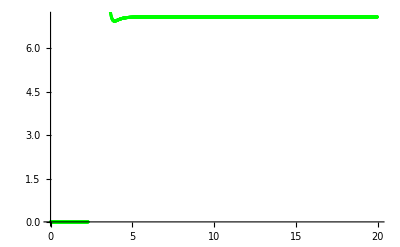

```mathematica
Show[{ListPlot[Table[{Ntab[[i]],Log[G11Deco[pref,kphys0*Exp[-Ntab[[i]]],lE*H,xstarref,kgamref]/G11[kphys0*Exp[-Ntab[[i]]]]]},{i,1,Length[Ntab]}],PlotStyle-> Green]}]
```

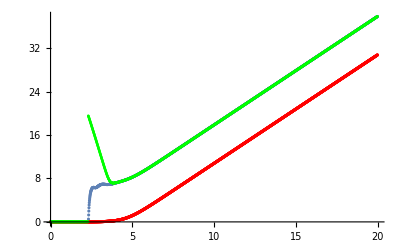

```mathematica
Show[{ListPlot[Table[{Ntab [[i]],Log[Re[Gamma11[[i]]]]},{i,1,Length[Ntab]}],PlotRange-> Full],ListPlot[Table[{Ntab[[i]],Log[G11[kphys0*Exp[-Ntab[[i]]]]]},{i,1,Length[Ntab]}],PlotStyle-> Red],
ListPlot[Table[{Ntab[[i]],Log[G11Deco[pref,kphys0*Exp[-Ntab[[i]]],lE*H,xstarref,kgamref]]},{i,1,Length[Ntab]}],PlotStyle-> Green]}]
```

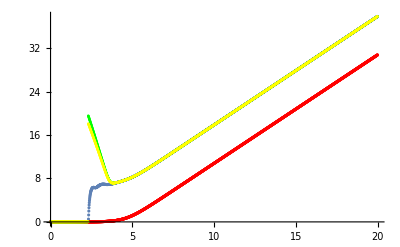

```mathematica
Show[{ListPlot[Table[{Ntab [[i]],Log[Re[Gamma11[[i]]]]},{i,1,Length[Ntab]}],PlotRange-> Full],ListPlot[Table[{Ntab[[i]],Log[G11[kphys0*Exp[-Ntab[[i]]]]]},{i,1,Length[Ntab]}],PlotStyle-> Red],
ListPlot[Table[{Ntab[[i]],Log[G11Deco[pref,kphys0*Exp[-Ntab[[i]]],lE*H,xstarref,kgamref]]},{i,1,Length[Ntab]}],PlotStyle-> Green],
ListPlot[Table[{Ntab[[i]],Log[G11DecoMod[pref,kphys0*Exp[-Ntab[[i]]],lE*H,xstarref,kgamref]]},{i,1,Length[Ntab]}],PlotStyle->Yellow]}]
```

```mathematica
γ12
```

```mathematica
G12Deco[p_,x_,lEH_,xstar_,kgam_]:=G12[x]-0.5*(kgam/k0)^2*(I12[p,x,lEH,xstar])*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]
```

```mathematica
G12DecoMod[p_,x_,lEH_,xstar_,kgam_]:=G12[x]-0.5*(kgam/k0)^2*(λ12Exact[p,x,lEH,xstar]+μ12[p,x,lEH,xstar])*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]
```

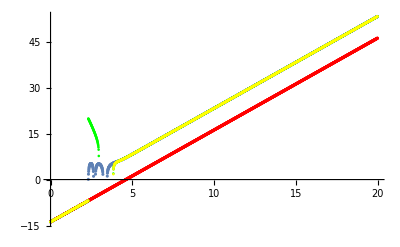

```mathematica
Show[{ListPlot[Table[{Ntab [[i]],Log[Re[Gamma12[[i]]]]},{i,1,Length[Ntab]}],PlotRange-> Full],ListPlot[Table[{Ntab[[i]],Log[G12[kphys0*Exp[-Ntab[[i]]]]]},{i,1,Length[Ntab]}],PlotStyle-> Red],
ListPlot[Table[{Ntab[[i]],Log[G12Deco[pref,kphys0*Exp[-Ntab[[i]]],lE*H,xstarref,kgamref]]},{i,1,Length[Ntab]}],PlotStyle-> Green],
ListPlot[Table[{Ntab[[i]],Log[G12DecoMod[pref,kphys0*Exp[-Ntab[[i]]],lE*H,xstarref,kgamref]]},{i,1,Length[Ntab]}],PlotStyle->Yellow]}]
```

```mathematica
γ22
```

```mathematica
G22Deco[p_,x_,lEH_,xstar_,kgam_]:=G22[x]-0.5*(kgam/k0)^2*(I22[p,x,lEH,xstar]+(1-2/(x^2))*I11[p,x,lEH,xstar])*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]
```

```mathematica
G22DecoMod[p_,x_,lEH_,xstar_,kgam_]:=G22[x]-0.5*(kgam/k0)^2*(λ22Exact[p,x,lEH,xstar]+μ22[p,x,lEH,xstar]+(1-2/(x^2))*(λ11Exact[p,x,lEH,xstar]+μ11[p,x,lEH,xstar]))*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]
```

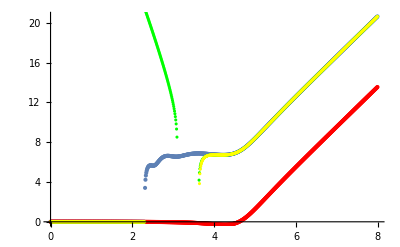

```mathematica
Show[{ListPlot[Table[{Ntab [[i]],Log[Re[Gamma22[[i]]]]},{i,1,Length[Ntab]}],PlotRange-> Full],ListPlot[Table[{Ntab[[i]],Log[G22[kphys0*Exp[-Ntab[[i]]]]]},{i,1,Length[Ntab]}],PlotStyle-> Red],
ListPlot[Table[{Ntab[[i]],Log[G22Deco[pref,kphys0*Exp[-Ntab[[i]]],lE*H,xstarref,kgamref]]},{i,1,Length[Ntab]}],PlotStyle-> Green],
ListPlot[Table[{Ntab[[i]],Log[G22DecoMod[pref,kphys0*Exp[-Ntab[[i]]],lE*H,xstarref,kgamref]]},{i,1,Length[Ntab]}],PlotStyle->Yellow]}]
```

## σ elegant version

```mathematica
(*For de Sitter the integral Lk is evaluated exactly *)
Lk[p_,x_,lEH_]:=x^(4-p)/(p-4)+x^(2-p)/(p-2)-(lEH)^(p-4)/(p-4)-(lEH)^(p-2)/(p-2)
```

```mathematica
k=15;
```

```mathematica
(*For α = 1-p. Starts at 1+1-p goes until 1+k+2-p *)
Mk2111[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k+2}]]]],α>0&&x>0]
```

```mathematica
Collect[Mk2111[1-p,x,lEH],x,Simplify]
```

x^(2-p)/(2-p)+(2 x^(4-p))/(-4+p)+(2 x^(6-p))/(18-3 p)+(4 x^(8-p))/(45 (-8+p))-(2 x^(10-p))/(315 (-10+p))+(4 x^(12-p))/(14175 (-12+p))-(4 x^(14-p))/(467775 (-14+p))+(8 x^(16-p))/(42567525 (-16+p))-(2 x^(18-p))/(638512875 (-18+p))+2^(-2+p) Cos[(p π)/2] Gamma[2-p]

```mathematica
(*For α = 3-p. Starts at 1+3-p goes until 3+k-p*)
Mk2112[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k}]]]],α>0&&x>0]
```

```mathematica
Collect[Mk2112[3-p,x,lEH],x,Simplify]
```

x^(4-p)/(4-p)+(2 x^(6-p))/(-6+p)+(2 x^(8-p))/(24-3 p)+(4 x^(10-p))/(45 (-10+p))-(2 x^(12-p))/(315 (-12+p))+(4 x^(14-p))/(14175 (-14+p))-(4 x^(16-p))/(467775 (-16+p))+(8 x^(18-p))/(42567525 (-18+p))-2^(-4+p) Cos[(p π)/2] Gamma[4-p]

```mathematica
(*For α = 2-p. Starts at 2+2-p goes until 2-p+k+1 (in fact 2-p+k+1+1 but it vanishes) *)
Mk2113[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k+1}]]]],α>0&&x>0]
```

```mathematica
Collect[Mk2113[2-p,x,lEH],x,Simplify]
```

-(2 x^(4-p))/(-4+p)+(4 x^(6-p))/(3 (-6+p))-(4 x^(8-p))/(15 (-8+p))+(8 x^(10-p))/(315 (-10+p))-(4 x^(12-p))/(2835 (-12+p))+(8 x^(14-p))/(155925 (-14+p))-(8 x^(16-p))/(6081075 (-16+p))+(16 x^(18-p))/(638512875 (-18+p))-2^(-3+p) (-2+p) Cos[(p π)/2] Gamma[2-p]

```mathematica
Mk211[p_,x_,lEH_]:=-Mk2111[1-p,x,lEH]+Mk2112[3-p,x,lEH]-2*Mk2113[2-p,x,lEH]
```

```mathematica
Mk212[p_,x_,lEH_]:=Evaluate@FullSimplify[-Re[ComplexExpand[(-2*I)^(-(1+1-p))*Gamma[1+1-p,-2*I/lEH]]]+Re[ComplexExpand[(-2*I)^(-(1+3-p))*Gamma[1+3-p,-2*I/lEH]]]-2*Im[ComplexExpand[(-2*I)^(-(1+2-p))*Gamma[1+2-p,-2*I/lEH]]],p>0&&lEH>0]
```

```mathematica
Mk21[p_,x_,lEH_]:=Mk211[p,x,lEH]+Mk212[p,x,lEH]
```

```mathematica
(*For α = 1-p. Starts at 2+1-p goes until 1-p+k+2 (which vanishes so 1-p+k+1) *)
Mk2211[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k+2}]]]],α>0&&x>0]
```

```mathematica
Collect[Mk2211[1-p,x,lEH],x,Simplify]
```

-(2 x^(3-p))/(-3+p)+(4 x^(5-p))/(3 (-5+p))-(4 x^(7-p))/(15 (-7+p))+(8 x^(9-p))/(315 (-9+p))-(4 x^(11-p))/(2835 (-11+p))+(8 x^(13-p))/(155925 (-13+p))-(8 x^(15-p))/(6081075 (-15+p))+(16 x^(17-p))/(638512875 (-17+p))+2^(-2+p) (-1+p) Gamma[1-p] Sin[(p π)/2]

```mathematica
(*For α = 3-p. Starts at 2+3-p goes until 3-p+k (which vanishes so 3-p+k-1) *)
Mk2212[α_,x_,lEH_]:=Evaluate@FullSimplify[Im[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k}]]]],α>0&&x>0]
```

```mathematica
Collect[Mk2212[3-p,x,lEH],x,Simplify]
```

-(2 x^(5-p))/(-5+p)+(4 x^(7-p))/(3 (-7+p))-(4 x^(9-p))/(15 (-9+p))+(8 x^(11-p))/(315 (-11+p))-(4 x^(13-p))/(2835 (-13+p))+(8 x^(15-p))/(155925 (-15+p))-(8 x^(17-p))/(6081075 (-17+p))-2^(-4+p) (-3+p) Gamma[3-p] Sin[(p π)/2]

```mathematica
(*For α = 2-p. Starts at 1+2-p goes until 2-p+k+1 (which vanishes so 2-p+k) *)
Mk2213[α_,x_,lEH_]:=Evaluate@FullSimplify[Re[ComplexExpand[Normal[Series[-(-2*I)^(-(1+α))*Gamma[1+α,-2*I*x],{x,0,k+1}]]]],α>0&&x>0]
```

```mathematica
Collect[Mk2213[2-p,x,lEH],x,Simplify]
```

x^(3-p)/(3-p)+(2 x^(5-p))/(-5+p)+(2 x^(7-p))/(21-3 p)+(4 x^(9-p))/(45 (-9+p))-(2 x^(11-p))/(315 (-11+p))+(4 x^(13-p))/(14175 (-13+p))-(4 x^(15-p))/(467775 (-15+p))+(8 x^(17-p))/(42567525 (-17+p))+2^(-3+p) Gamma[3-p] Sin[(p π)/2]

```mathematica
Mk221[p_,x_,lEH_]:=-Mk2211[1-p,x,lEH]+Mk2212[3-p,x,lEH]+2*Mk2213[2-p,x,lEH]
```

```mathematica
Mk222[p_,x_,lEH_]:=Evaluate@FullSimplify[-Im[ComplexExpand[(-2*I)^(-(1+1-p))*Gamma[1+1-p,-2*I/lEH]]]+Im[ComplexExpand[(-2*I)^(-(1+3-p))*Gamma[1+3-p,-2*I/lEH]]]+2*Re[ComplexExpand[(-2*I)^(-(1+2-p))*Gamma[1+2-p,-2*I/lEH]]],p>0&&lEH>0]
```

```mathematica
Mk22[p_,x_,lEH_]:=Mk221[p,x,lEH]+Mk222[p,x,lEH]
```

```mathematica
(*Compute approximation for the combination entering the expression of Sig(0)^2 at quadractic order in perturbations. Cancellations makes it non-trivial to find the leading term*)
Collect[(Lk[p,x,lEH])^2-(Mk21[p,x,lEH])^2-(Mk22[p,x,lEH])^2,x^_,Simplify]
```

(4 x^(10-2 p))/((-8+p) (-5+p)^2 (-2+p))-(16 x^(12-2 p))/((-10+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))+(64 x^(14-2 p))/((-12+p) (-10+p) (-9+p) (-7+p)^2 (-5+p) (-4+p) (-2+p))-(256 x^(16-2 p))/((-14+p) (-12+p) (-11+p) (-9+p) (-8+p)^2 (-7+p) (-5+p) (-4+p) (-2+p))+(1024 x^(18-2 p))/((-16+p) (-14+p) (-13+p) (-11+p) (-10+p) (-9+p)^2 (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-(4096 x^(20-2 p))/((-18+p) (-16+p) (-15+p) (-13+p) (-12+p) (-11+p) (-10+p)^2 (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))+(4 (-286000/(-11+p)^2-405/(72-22 p+p^2)+1848/(85-22 p+p^2)-27216/(105-22 p+p^2)+120120/(112-22 p+p^2)-294840/(117-22 p+p^2)+486486/(120-22 p+p^2)) x^(22-2 p))/5746615875+(4 (-104247/(-12+p)^2+3696/(119-24 p+p^2)-19500/(128-24 p+p^2)+58320/(135-24 p+p^2)-120120/(140-24 p+p^2)+182000/(143-24 p+p^2)) x^(24-2 p))/28733079375+(8 (-31850/(-13+p)^2+2475/(144-26 p+p^2)-8712/(153-26 p+p^2)+21450/(160-26 p+p^2)-39600/(165-26 p+p^2)+56628/(168-26 p+p^2)) x^(26-2 p))/316063873125+(8 (-88088/(-14+p)^2-31185/(180-28 p+p^2)+67760/(187-28 p+p^2)-115830/(192-28 p+p^2)+158760/(195-28 p+p^2)) x^(28-2 p))/19912024006875+(8 (-40824/(-15+p)^2+34749/(216-30 p+p^2)-56056/(221-30 p+p^2)+74360/(224-30 p+p^2)) x^(30-2 p))/258856312089375+(16 (-21125/(-16+p)^2-30030/(252-32 p+p^2)+38808/(255-32 p+p^2)) x^(32-2 p))/9059970923128125+(16 (-23716/(-17+p)^2+43875/(288-34 p+p^2)) x^(34-2 p))/407698691540765625-(4 x^(36-2 p))/(201332687180625 (-18+p)^2)+1/(45 (-10+p))2^(-2+p) x^(10-p) (Cos[(p π)/2] (-4 (-3+p) Gamma[2-p]+Gamma[4-p])-Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]-Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(14189175 (-18+p))2^(-2+p) x^(18-p) (Cos[(p π)/2] (-4 (-3+p) Gamma[2-p]+Gamma[4-p])-Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]-Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(9 (-8+p))2^(-2+p) x^(8-p) (Cos[(p π)/2] (4 (-3+p) Gamma[2-p]-Gamma[4-p])+Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(525 (-12+p))2^(-2+p) x^(12-p) (Cos[(p π)/2] (4 (-3+p) Gamma[2-p]-Gamma[4-p])+Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])-1/(42525 (-14+p))2^p x^(14-p) (Cos[(p π)/2] (4 (-3+p) Gamma[2-p]-Gamma[4-p])+Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/(654885 (-16+p))2^(-1+p) x^(16-p) (Cos[(p π)/2] (4 (-3+p) Gamma[2-p]-Gamma[4-p])+Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])+1/8 x^(4-p) (-(16 lEH^(-4+p))/(-4+p)^2-(16 lEH^(-2+p))/(8-6 p+p^2)+(3 2^(2+p) Cos[(p π)/2] Gamma[2-p])/(-4+p)+(2^(2+p) p Cos[(p π)/2] Gamma[2-p])/(4-p)+(2^p Cos[(p π)/2] Gamma[4-p])/(-4+p)-(2^p Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]])/(-4+p)-(2^p Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/(-4+p))+1/8 x^(2-p) (-(16 lEH^(-2+p))/(-2+p)^2-(16 lEH^(-4+p))/(8-6 p+p^2)+(3 2^(2+p) Cos[(p π)/2] Gamma[2-p])/(-2+p)+(2^(2+p) p Cos[(p π)/2] Gamma[2-p])/(2-p)+(2^p Cos[(p π)/2] Gamma[4-p])/(-2+p)-(2^p Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]])/(-2+p)-(2^p Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/(-2+p))+1/(35 (-9+p))2^(-1+p) x^(9-p) (Cos[(p π)/2] Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]-(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]+Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]) Sin[(p π)/2])+1/(4455 (-13+p))2^(-1+p) x^(13-p) (Cos[(p π)/2] Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]-(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]+Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]) Sin[(p π)/2])+1/(8292375 (-17+p))2^p x^(17-p) (Cos[(p π)/2] Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]-(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]+Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]) Sin[(p π)/2])+1/(3 (-5+p))2^(-2+p) x^(5-p) (-Cos[(p π)/2] Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]+Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]) Sin[(p π)/2])+1/(15 (-7+p))2^(-1+p) x^(7-p) (-Cos[(p π)/2] Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]+Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]) Sin[(p π)/2])+1/(567 (-11+p))2^p x^(11-p) (-Cos[(p π)/2] Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]+Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]) Sin[(p π)/2])+1/(225225 (-15+p))2^p x^(15-p) (-Cos[(p π)/2] Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]+Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]) Sin[(p π)/2])+1/256 ((256 lEH^(-8+2 p))/(-4+p)^2+(256 lEH^(-4+2 p))/(-2+p)^2+(512 lEH^(-6+2 p))/(8-6 p+p^2)-9 4^(2+p) Cos[(p π)/2]^2 Gamma[2-p]^2+3 2^(5+2 p) p Cos[(p π)/2]^2 Gamma[2-p]^2-4^(2+p) p^2 Cos[(p π)/2]^2 Gamma[2-p]^2-3 2^(3+2 p) Cos[(p π)/2]^2 Gamma[2-p] Gamma[4-p]+2^(3+2 p) p Cos[(p π)/2]^2 Gamma[2-p] Gamma[4-p]-4^p Cos[(p π)/2]^2 Gamma[4-p]^2-4^p Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]^2-4^p Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]^2-4^(2+p) Gamma[1-p]^2 Sin[(p π)/2]^2+2^(5+2 p) p Gamma[1-p]^2 Sin[(p π)/2]^2-4^(2+p) p^2 Gamma[1-p]^2 Sin[(p π)/2]^2-7 2^(3+2 p) Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2+4^(3+p) p Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2-2^(3+2 p) p^2 Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2-49 4^p Gamma[3-p]^2 Sin[(p π)/2]^2+7 2^(1+2 p) p Gamma[3-p]^2 Sin[(p π)/2]^2-4^p p^2 Gamma[3-p]^2 Sin[(p π)/2]^2-2^(1+2 p) Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] (4 (-3+p) Cos[(p π)/2]^2 Gamma[2-p]-Cos[(p π)/2]^2 Gamma[4-p]+(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]) Sin[(p π)/2]^2)+4^p (4 (-1+p) Gamma[1-p]-4 (-3+p) Gamma[2-p]-7 Gamma[3-p]+p Gamma[3-p]+Gamma[4-p]) Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[p π])

```mathematica
Coeff2Minusp[p_,x_,lEH_]:=1/8  (-(16 lEH^(-2+p))/(-2+p)^2-(16 lEH^(-4+p))/(8-6 p+p^2)+(3 2^(2+p) Cos[(p π)/2] Gamma[2-p])/(-2+p)+(2^(2+p) p Cos[(p π)/2] Gamma[2-p])/(2-p)+(2^p Cos[(p π)/2] Gamma[4-p])/(-2+p)-(2^p Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]])/(-2+p)-(2^p Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/(-2+p))
```

```mathematica
FullSimplify[(3 2^(2+p) Cos[(p π)/2] Gamma[2-p])/(-2+p)+(2^(2+p) p Cos[(p π)/2] Gamma[2-p])/(2-p)+(2^p Cos[(p π)/2] Gamma[4-p])/(-2+p)]
```

(2^p (-6+p) Cos[(p π)/2] Gamma[4-p])/(-2+p)^2

```mathematica
FullSimplify[8-6 p+p^2]
```

(-4+p) (-2+p)

```mathematica
Simplify[ComplexExpand[Normal[Series[-(2^p Cos[(p π)/2] Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]])/(-2+p)-(2^p Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[(p π)/2])/(-2+p),{lEH,0,0}]]],lEH>0&&p>0]
```

(lEH^(-3+p) (-4 lEH (-7+p) Cos[2/lEH]+8 Sin[2/lEH]))/(-2+p)

```mathematica
CoeffCst[p_,x_,lEH_]:=1/256 ((256 lEH^(-8+2 p))/(-4+p)^2+(256 lEH^(-4+2 p))/(-2+p)^2+(512 lEH^(-6+2 p))/(8-6 p+p^2)-9 4^(2+p) Cos[(p π)/2]^2 Gamma[2-p]^2+3 2^(5+2 p) p Cos[(p π)/2]^2 Gamma[2-p]^2-4^(2+p) p^2 Cos[(p π)/2]^2 Gamma[2-p]^2-3 2^(3+2 p) Cos[(p π)/2]^2 Gamma[2-p] Gamma[4-p]+2^(3+2 p) p Cos[(p π)/2]^2 Gamma[2-p] Gamma[4-p]-4^p Cos[(p π)/2]^2 Gamma[4-p]^2-4^p Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]^2-4^p Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]^2-4^(2+p) Gamma[1-p]^2 Sin[(p π)/2]^2+2^(5+2 p) p Gamma[1-p]^2 Sin[(p π)/2]^2-4^(2+p) p^2 Gamma[1-p]^2 Sin[(p π)/2]^2-7 2^(3+2 p) Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2+4^(3+p) p Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2-2^(3+2 p) p^2 Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2-49 4^p Gamma[3-p]^2 Sin[(p π)/2]^2+7 2^(1+2 p) p Gamma[3-p]^2 Sin[(p π)/2]^2-4^p p^2 Gamma[3-p]^2 Sin[(p π)/2]^2-2^(1+2 p) Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] (4 (-3+p) Cos[(p π)/2]^2 Gamma[2-p]-Cos[(p π)/2]^2 Gamma[4-p]+(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]) Sin[(p π)/2]^2)+4^p (4 (-1+p) Gamma[1-p]-4 (-3+p) Gamma[2-p]-7 Gamma[3-p]+p Gamma[3-p]+Gamma[4-p]) Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[p π])
```

```mathematica
Simplify[ComplexExpand[Normal[Series[4^p Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]^2-4^p Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]^2+2^(1+2 p) Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]-2^(1+2 p) Re[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]]+Im[4 (Gamma[2-p,-(2 ⅈ)/lEH]+Gamma[3-p,-(2 ⅈ)/lEH])+Gamma[4-p,-(2 ⅈ)/lEH]] Sin[p π],{lEH,0,0}]]],lEH>0&&p>0]
```

2^(1-p) lEH^(-6+p) (lEH^4 (-7+p) Cos[2/lEH-(p π)/2]-2^(3+p) lEH^p (-4+lEH^2 (-7+p)^2) Cos[4/lEH+p π]-lEH^4 (-7+p) Cos[2/lEH+(3 p π)/2]+4 lEH Cos[2/lEH+(p π)/2] (lEH^2 Sin[p π]+2^(4+p) lEH^p (-7+p) Sin[2/lEH+(p π)/2]))

```mathematica
2^(3-p) lEH^(-3+p)  Cos[2/lEH+(p π)/2]  Sin[p π]
```

```mathematica
FullSimplify[-9 4^(2+p) Cos[(p π)/2]^2 Gamma[2-p]^2+3 2^(5+2 p) p Cos[(p π)/2]^2 Gamma[2-p]^2-4^(2+p) p^2 Cos[(p π)/2]^2 Gamma[2-p]^2-3 2^(3+2 p) Cos[(p π)/2]^2 Gamma[2-p] Gamma[4-p]+2^(3+2 p) p Cos[(p π)/2]^2 Gamma[2-p] Gamma[4-p]-4^p Cos[(p π)/2]^2 Gamma[4-p]^2+(4 (-3+p) Cos[(p π)/2]^2 Gamma[2-p]-Cos[(p π)/2]^2 Gamma[4-p]+(4 (-1+p) Gamma[1-p]+(-7+p) Gamma[3-p]) Sin[(p π)/2]^2)+4^p (4 (-1+p) Gamma[1-p]-4 (-3+p) Gamma[2-p]-7 Gamma[3-p]+p Gamma[3-p]+Gamma[4-p]-4^(2+p) Gamma[1-p]^2 Sin[(p π)/2]^2+2^(5+2 p) p Gamma[1-p]^2 Sin[(p π)/2]^2-4^(2+p) p^2 Gamma[1-p]^2 Sin[(p π)/2]^2-7 2^(3+2 p) Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2+4^(3+p) p Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2-2^(3+2 p) p^2 Gamma[1-p] Gamma[3-p] Sin[(p π)/2]^2-49 4^p Gamma[3-p]^2 Sin[(p π)/2]^2+7 2^(1+2 p) p Gamma[3-p]^2 Sin[(p π)/2]^2-4^p p^2 Gamma[3-p]^2 Sin[(p π)/2]^2) ]
```

((-6+p) Gamma[4-p] (4-2 p+4^p (-6+p) (-1-4^p+(-1+4^p) Cos[p π]) Gamma[4-p]))/(2 (-2+p)^2)

```mathematica
(*Express the integrals using the de Sitter approximation. Expanding to order k in x and p-1+klEH in lEH we get expressions valid up to order k+2-p in x and *)
```

```mathematica
Lk[p_,x_,lEH_,xstar_] :=(xstar^(p-3))*((x^(2-p))/(2-p)+(x^(4-p))/(4-p) -  (lEH^(p-2))/(2-p)- (lEH^(p-4))/(4-p)) ;
Mk2[p_,x_,lEH_,xstar_] :=(xstar^(2p-6))*((Mk21[p,x,lEH])^2+(Mk22[p,x,lEH])^2) ;
```

```mathematica
Sigma2Elegant[p_,x_,lEH_,xstar_,kgam_]:= 1-(kgam/k0)^2*Lk[p,x,lEH,xstar]*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]+0.25*0.25*(kgam/k0)^4*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]*(Lk[p,x,lEH,xstar]^2-Mk2[p,x,lEH,xstar])
```

```mathematica
Sigma2Elegant[p_,x_,lEH_,xstar_,kgam_]:= 1-(kgam/k0)^2*Lk[p,x,lEH,xstar]*HeavisideTheta[N0-Log[x/kphys0]-Ncrossref]
```

To have the same number of points as in Python we stop before the last index

```mathematica
ptest=6.01;
Sigma2ElegantArray = Table[Sigma2Elegant[6.1,kphys0*Exp[-(n)],lE*H,1,kgamref],{n,0,15-deltaN,deltaN}];
Export[StringJoin[{"Data/Sigma2ElegantArrayp",ToString[NumberForm[ptest,NumberPoint->","]],".fits"}],Sigma2ElegantArray]
```

Data/Sigma2ElegantArrayp6,01.fits

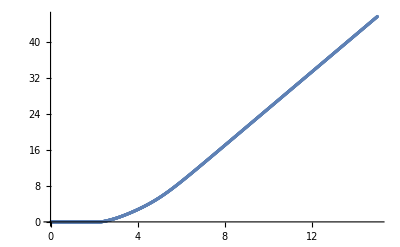

```mathematica
ListPlot[Table[{i*deltaN,Log[Sigma2ElegantArray[[i]]]},{i,1,Length[Sigma2ElegantArray]}]]
```

```mathematica
(*Expression without difference with the decoherence term expanded. This does not cause numerical problem.*)
Sigma2ElegantTheta[p_,x_,lEH_,xstar_,kgam_,θ_]:=Evaluate@Cos[2*θ]^2*Sigma2Elegant[p,x,lEH,xstar,kgam]+Sin[2*θ]^2*(G11Deco[p,x,lEH,xstar,kgam]+G22Deco[p,x,lEH,xstar,kgam])^2/4
```

## Discord

Function necessary to compute the Discord

```mathematica
f[x_]:=If[x≤1,0,If[x<1000,(x+1)*Log[(x+1)/2]/Log[2]/2-(x-1)*Log[(x-1)/2]/Log[2]/2,Log[x/2]/Log[2]+1/Log[2]]]
```

```mathematica
(*We compare an approximation of the discord by its dominant term to compare it with the value obtained using the full sigma modified containing several terms*)
```

```mathematica
Collect[λ22[p,x,lEH,xstar]+μ22[p,x,lEH,xstar]+(1-2/x^2)*( λ11[p,x,lEH,xstar]+μ11[p,x,lEH,xstar]),x^_,Simplify]
```

-((26-11 p+p^2) x^(4-p) xstar^(-3+p))/((-8+p) (-5+p) (-2+p))+(2 (-344+146 p-21 p^2+p^3) x^(6-p) xstar^(-3+p))/((-10+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))-(8 (-728+242 p-27 p^2+p^3) x^(8-p) xstar^(-3+p))/((-12+p) (-10+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))+(32 (128-22 p+p^2) x^(10-p) xstar^(-3+p))/((-14+p) (-12+p) (-10+p) (-9+p) (-8+p) (-7+p) (-5+p) (-4+p) (-2+p))+(x^2 xstar^(-3+p) (-2^(2+p) lEH^3 (-3+p) Cos[(p π)/2] Gamma[2-p]+2^p lEH^3 Cos[(p π)/2] Gamma[4-p]-2 lEH^p (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))/(36 lEH^3)+(x^4 xstar^(-3+p) (2^(2+p) lEH^3 (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p lEH^3 Cos[(p π)/2] Gamma[4-p]+2 lEH^p (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))/(90 lEH^3)-(43 x^6 xstar^(-3+p) (2^(2+p) lEH^3 (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p lEH^3 Cos[(p π)/2] Gamma[4-p]+2 lEH^p (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))/(25200 lEH^3)+(67 x^8 xstar^(-3+p) (2^(2+p) lEH^3 (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p lEH^3 Cos[(p π)/2] Gamma[4-p]+2 lEH^p (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))/(498960 lEH^3)-(113 x^10 xstar^(-3+p) (2^(2+p) lEH^3 (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p lEH^3 Cos[(p π)/2] Gamma[4-p]+2 lEH^p (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))/(16216200 lEH^3)+(x^12 xstar^(-3+p) (2^(2+p) lEH^3 (-3+p) Cos[(p π)/2] Gamma[2-p]-2^p lEH^3 Cos[(p π)/2] Gamma[4-p]+2 lEH^p (2 lEH (-7+p) Cos[2/lEH]+(-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))/(2702700 lEH^3)+1/(32 lEH^4 (-4+p) (-2+p) x^2)xstar^(-3+p) (-2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]+2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]-2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/(32 lEH^4 (-4+p) (-2+p))xstar^(-3+p) (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+1/(32 lEH^4 (-4+p) (-2+p) x^4)xstar^(-3+p) (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))+(x^13 xstar^(-3+p) (-2 lEH^p ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])-2^(2+p) lEH^3 (-1+p) Gamma[1-p] Sin[(p π)/2]-2^p lEH^3 (-7+p) Gamma[3-p] Sin[(p π)/2]))/(12162150 lEH^3)+(xstar^(-3+p) (2 lEH^p ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) lEH^3 (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p lEH^3 (-7+p) Gamma[3-p] Sin[(p π)/2]))/(24 lEH^3 x)-(7 x xstar^(-3+p) (2 lEH^p ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) lEH^3 (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p lEH^3 (-7+p) Gamma[3-p] Sin[(p π)/2]))/(240 lEH^3)+(17 x^3 xstar^(-3+p) (2 lEH^p ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) lEH^3 (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p lEH^3 (-7+p) Gamma[3-p] Sin[(p π)/2]))/(840 lEH^3)-(109 x^5 xstar^(-3+p) (2 lEH^p ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) lEH^3 (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p lEH^3 (-7+p) Gamma[3-p] Sin[(p π)/2]))/(22680 lEH^3)+(16 x^7 xstar^(-3+p) (2 lEH^p ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) lEH^3 (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p lEH^3 (-7+p) Gamma[3-p] Sin[(p π)/2]))/(31185 lEH^3)-(23 x^9 xstar^(-3+p) (2 lEH^p ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) lEH^3 (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p lEH^3 (-7+p) Gamma[3-p] Sin[(p π)/2]))/(772200 lEH^3)+(19 x^11 xstar^(-3+p) (2 lEH^p ((-4+lEH^2 (18-9 p+p^2)) Cos[2/lEH]-2 lEH (-7+p) Sin[2/lEH])+2^(2+p) lEH^3 (-1+p) Gamma[1-p] Sin[(p π)/2]+2^p lEH^3 (-7+p) Gamma[3-p] Sin[(p π)/2]))/(24324300 lEH^3)

```mathematica
Clear[Coeff]
```

```mathematica
Coeff[p_,x_,lEH_,xstar_,kgam_] :=1-0.5*(kgam/k0)^2*1/(32 lEH^4 (-4+p) (-2+p))xstar^(-3+p) (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))
```

```mathematica
Coeff[2.1,1,0.1,xstarref,kgamref]
```

1195.53

```mathematica
Sigma2minp[p_,x_,lEH_,xstar_,kgam_] :=0.5*(kgam/k0)^2*xstar^(-3+p)/(2-p)+0.25*(kgam/k0)^4*1/(32 lEH^4 (-4+p) (-2+p)^2) xstar^(-6+2 p) (-2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]+2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]-2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH]))
```

```mathematica
DiscordApprox[p_,x_,lEH_,xstar_,kgam_,θ_]:= Log[1+x^(p-6)*Abs[Sin[2*θ]*Coeff[p,x,lEH,xstar,kgam]/Sigma2minp[p,x,lEH,xstar,kgam]]/2]/Log[2]
```

```mathematica
Series[(x+1)*Log[(x+1)/2]/Log[2]/2-(x-1)*Log[(x-1)/2]/Log[2]/2,{x,Infinity,3}]
```

(1-Log[2]+Log[x])/Log[2]-1/(6 Log[2] x^2)+O[1/x]^4

```mathematica
Discord[p_,x_,lEH_,xstar_,kgam_,θ_]:=f[Sqrt[Sig2ModThetaAltMod[p,x,lEH,xstar,kgam,θ]]]-2*f[Sqrt[Sig2Mod[p,x,lEH,xstar,kgam]]]+f[(Sqrt[Sig2ModThetaAltMod[p,x,lEH,xstar,kgam,θ]]+Sig2Mod[p,x,lEH,xstar,kgam])/(Sqrt[Sig2ModThetaAltMod[p,x,lEH,xstar,kgam,θ]]+1)]
```

```mathematica
DiscordElegant[p_,x_,lEH_,xstar_,kgam_,θ_]:=Evaluate@f[Sqrt[Sigma2ElegantTheta[p,x,lEH,xstar,kgam,θ]]]-2*f[Sqrt[Sigma2Elegant[p,x,lEH,xstar,kgam]]]+f[(Sqrt[Sigma2ElegantTheta[p,x,lEH,xstar,kgam,θ]]+Sigma2Elegant[p,x,lEH,xstar,kgam])/(Sqrt[Sigma2ElegantTheta[p,x,lEH,xstar,kgam,θ]]+1)]
```

```mathematica
DiscordElegant[pref,kphys0*Exp[-Ntab3[[500]]],lE*H,xstarref,kgamref,Pi/4]
```

27.539

```mathematica
Ntab3=Table[i,{i,N0+5,20,0.1}];
```

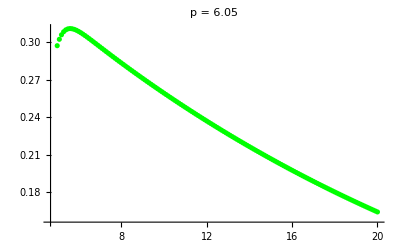

```mathematica
ptest = 6.05;
Show[{
ListPlot[Table[{Ntab3[[i]],DiscordElegant[ptest,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab3]}],PlotStyle-> Green,PlotRange-> Full,PlotLabel-> StringJoin["p = ",ToString[ptest]]]}]
```

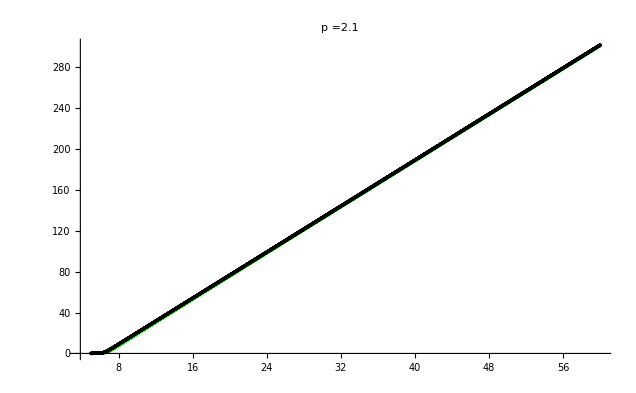

```mathematica
Show[{
ListPlot[Table[{Ntab3[[i]],Discord[pref,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab3]}],PlotStyle-> Green,PlotRange-> Full,PlotLabel-> StringJoin["p =",ToString[pref]]],
ListPlot[Table[{Ntab3[[i]],DiscordApprox[pref,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab3]}],PlotStyle-> Black]}]
```

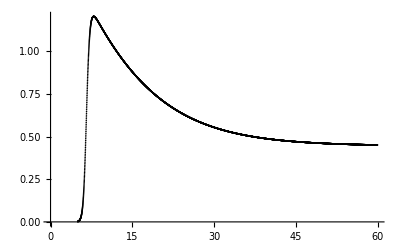

```mathematica
ListPlot[Table[{Ntab3[[i]],DiscordApprox[pref,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]-Discord[pref,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab3]}],PlotStyle-> Black]
```

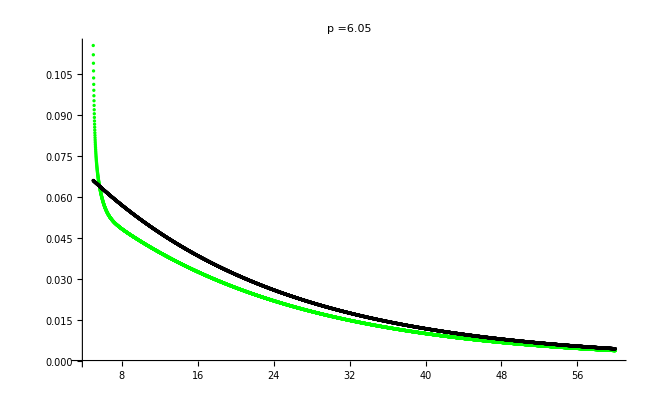

```mathematica
Show[{
ListPlot[Table[{Ntab3[[i]],Discord[6.05,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab3]}],PlotStyle-> Green,PlotRange-> Full,PlotLabel-> StringJoin["p =",ToString[6.05]]],
ListPlot[Table[{Ntab3[[i]],DiscordApprox[6.05,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab3]}],PlotStyle-> Black]}]
```

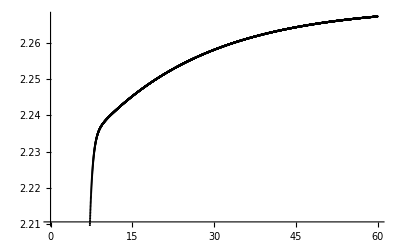

```mathematica
ListPlot[Table[{Ntab3[[i]],DiscordApprox[6.05,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]/Discord[6.05,kphys0*Exp[-Ntab3[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab3]}],PlotStyle-> Black]
```

```mathematica
Show[{
ListPlot[Table[{Ntab2[[i]],Discord[6.05,kphys0*Exp[-Ntab2[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab2]}],PlotStyle-> Green,PlotRange-> Full]}]
```

```mathematica
Show[{
ListPlot[Table[{Ntab2[[i]],Discord[pref,kphys0*Exp[-Ntab2[[i]]],lE*H,xstarref,kgamref,Pi/4]},{i,1,Length[Ntab2]}],PlotStyle-> Green,PlotRange-> Full]}]
```

```mathematica
Collect[G22[x]-(kgam/k)^2*(1/(32 lEH^4 (-4+p) (-2+p) x^4)3 xstar^(-3+p) (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))/2,x^_, Simplify]
```

1-1/x^2+1/x^4(1-1/(64 k^2 lEH^4 (-4+p) (-2+p))3 kgam^2 xstar^(-3+p) (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))

```mathematica
Collect[-32*2*(1/(64 k^2 lEH^4 (-4+p) (-2+p))3 kgam^2 xstar^(-3+p) (2^(2+p) lEH^4 (-24+26 p-9 p^2+p^3) Cos[(p π)/2] Gamma[2-p]-2^p lEH^4 (8-6 p+p^2) Cos[(p π)/2] Gamma[4-p]+2 lEH^p (8 (-2+lEH^2 (-4+p)+p)+2 lEH^2 (-56+50 p-13 p^2+p^3) Cos[2/lEH]+lEH (8-6 p+p^2) (-4+lEH^2 (18-9 p+p^2)) Sin[2/lEH])))/(kgam/k)^2/xstar^(-3+p) ,lEH^_,FullSimplify]
```

-(48 lEH^(-4+p))/(-4+p)+lEH^(-2+p) (-48/(-2+p)-12 (-7+p) Cos[2/lEH])+(3 2^p (-6+p) Cos[(p π)/2] Gamma[4-p])/(-2+p)+24 lEH^(-3+p) Sin[2/lEH]-6 lEH^(-1+p) (-6+p) (-3+p) Sin[2/lEH]